Last modified:  25, April 25

# SWSE P-NP WKB Periods

## Configuration

Configuration adapted from P. Bourg

##### Keyboard shortcuts

The following allows to auto-replace stuff when you write “tex[” into “TeXForm[StandardForm[]]”,
	which is what is needed to  output LATEX code of an equation. The StandardForm is needed if using the notation package.

```mathematica
CurrentValue[EvaluationNotebook[],{InputAutoReplacements,"tex"}]=RowBox[{"TeXForm","■"}];
```

##### Palettes and docked buttons

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
(*CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]*)
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines shoul not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
				ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

##### Timestamp

This code puts a timestamp at the beginning of the document whenever one saves the notebook.

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{"WindowClose":>Module[{dy,mn,yr},{dy,mn,yr}=
	   Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]];
     LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Second"}];NotebookLocate["LastModified"];
	     NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy,", ",mn," ",yr}],"Text",CellTags->"LastModified"]]]}]
```

##### Option Inspector

We can set the notebook to automatically save upon closing. We however will not do that (made below unevaluable)! 
	We keep the code as a basis for possible future use.
	Due to the timestamp code above, this means that a “Save Changes To” windows will always appear.

```mathematica
CurrentValue[$FrontEndSession,"ClosingAutoSave"] = True
```

##### DumpSave load

As a rule of thumb, packages should be loaded before loading mx files, because the latter may depend on definitions from those packages.
	If no dumpsave exist, the below simply prints this fact and does not do anything else.

Note: The dump-file’s name is assumed to have the very same name for the current notebook, with the extension “.mx” instead of “.nb”.

```mathematica
(*With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],StringDelete[Last[FileNameSplit[NotebookFileName[]]],".nb"]}] <> ".mx"}, 
	If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]]*)
```

```mathematica
NotebookDirectory[]
```

/Users/antares/Library/CloudStorage/Dropbox/Physics projects/My NBs/Kerr/Harmonics WKB/

```mathematica
SetOptions[EvaluationNotebook[],Magnification->0.95]
```

## Global

```mathematica
WP = 64; (* working precision *)
PREC=128;
rootPrec= 48;
```

```mathematica
Γ[f_]:=Gamma[f] (* gamma helper *)
```

```mathematica
myEllipticK[k_]:= EllipticK[k^2]
myEllipticE[k_] := EllipticE[k^2]
myEllipticPi[m_,k_] := EllipticPi[m,k^2]
```

## Import packages and define assumptions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/antares/Library/CloudStorage/Dropbox/Physics projects/My NBs/Kerr/Harmonics WKB

```mathematica
Needs["SpinWeightedSpheroidalHarmonics`"]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
$Assumptions = mu0 ∈Reals && mu1 ∈ Reals && Ε>0 && EE>0 && μ1∈Reals && μ0 ∈Reals
```

mu0∈ℝ&&mu1∈ℝ&&Ε>0&&EE>0&&μ1∈ℝ&&μ0∈ℝ

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$Assumptions = Ω∈Reals&&Ω>1/2&&θp ∈ Reals && 0<θ ∈ π&& L>=0 && -L <= M <= L&&l>=0&&-l<=m<=l&& m ∈ Integers && l ∈Integers && L∈ Integers && ω∈ Reals;
```

-Graphics-

Note that the BHPT uses a different convention for the eigenvalue λ= K + 2cm

```mathematica
?SpinWeightedSpheroidalEigenvalue
```

```mathematica
Series[SpinWeightedSpheroidalEigenvalue[-2,2,2,γ],{γ,∞,6}]
```

-6 γ+3+3/(4 γ)-15/(64 γ^3)-3/(16 γ^4)+3/(512 γ^5)+27/(128 γ^6)+O[1/γ]^7

```mathematica
ClearAll[s,l,m,phi0,gammaVals,Sfun,Sfun0];

s=-2;
l=2;
m=2;
phi0=0;

(*pick 10 increasing gamma values;adjust the range as you like*)
gammaVals=SetPrecision[Subdivide[2,10,5],WP];

Sfun[γ_?NumericQ,θ_?NumericQ]:=SpinWeightedSpheroidalHarmonicS[s,l,m,γ][θ,phi0];
Sfun0[γ_?NumericQ,θ_?NumericQ]:=SpinWeightedSpheroidalHarmonicS[0,l,m,γ][θ,phi0];

Sfun0plot=Plot[Evaluate@Table[Re[Sfun[γ,θ]],{γ,gammaVals}],{θ,0,Pi},PlotRange->All,PlotPoints->32,MaxRecursion->5,Frame->True,FrameLabel->{Style["θ",14],Style["Re["<>ToString[TraditionalForm[Subscript[Style["S",Italic],""]]]<>"]",14]},PlotLegends->Placed[LineLegend[Table["γ = "<>ToString@NumberForm[N[γ,6],{4,1}],{γ,gammaVals}],LegendLabel->Style["s = -2, l = 2, m = 2",12]],Right],ImageSize->Large]
(*Sfun=Plot[Evaluate@Table[Re[Sfun[γ,θ]],{γ,gammaVals}],{θ,0,Pi},PlotRange->All,PlotPoints->32,MaxRecursion->5,Frame->True,FrameLabel->{Style["θ",14],Style["Re["<>ToString[TraditionalForm[Subscript[Style["S",Italic],""]]]<>"]",14]},PlotLegends->Placed[LineLegend[Table["γ = "<>ToString@NumberForm[N[γ,6],{4,1}],{γ,gammaVals}],LegendLabel->Style["s = -2, l = 2, m = 2",12]],Right],ImageSize->Large]*)
```

SpinWeightedSpheroidalHarmonicS::maxterms: Spin-weighted spheroidal harmonic cannot be computed to the requested accuracy using "Leaver" method with 200 terms and the given working precision. A more accurate result may be obtained by increasing the value for the "MaxTerms" suboption for the "Leaver" method.

General::stop: Further output of SpinWeightedSpheroidalHarmonicS::maxterms will be suppressed during this calculation.

$Aborted

```mathematica
Export["SOfc_spin0.pdf",Sfun0plot]
```

```mathematica
ClearAll[s,l,m,phi0,gammaVals,Sfun,Sfun0, Sfunplot,Sfun0plot]
```

## symmetric potential WKB (s=0 case)

The equation here we study is 
-hbar^2/2 ψ'' (θ) + (cos^2(θ)+μ^2 csc^2(θ) -E)ψ(θ) = 0
Here we explore the  perturbative and non-perturbative expan-
sions of the eigenvalue in the case −1 < μ < 0 as in https://arxiv.org/pdf/2503.06780
where the parameters are connected to the black hole params by

```mathematica
hbarToBH=hbar->ⅈ Sqrt[2]/(a ω);
EToBH=Ε->-1/(a ω)^2(λ+1/4); (* here λ is equivalent to A in Teukolsky  *)
μToBH=μ->1/(a ω)^2(1/4-m^2);
ToBH[g_]:= g/. {hbarToBH,EToBH,μToBH};
```

```mathematica
Vpot[θ_,μ_]:=Cos[θ]^2+μ Csc[θ]^2 (* s=0 spheroidal  potential *)
```

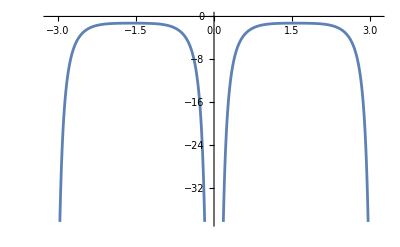

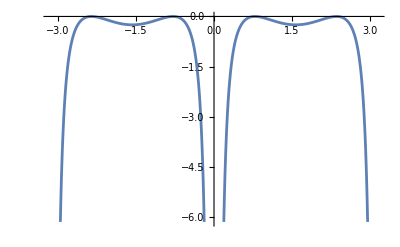

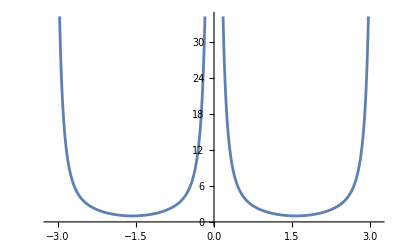

```mathematica
Plot[Vpot[th,-1.25],{th,-π,π}]
Plot[Vpot[th,-.25],{th,-π,π}]
Plot[Vpot[th,1],{th,-π,π}]
```

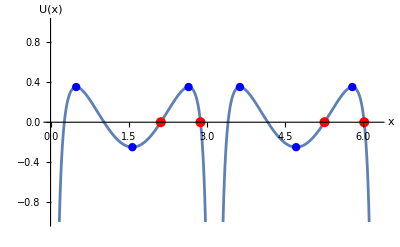

```mathematica
ClearAll[V,turningU,turningX,barrierX,eps,E0,mu];

U0[x_,E0_,mu_]:=Cos[x]^2+mu Csc[x]^2-E0;

turningU[E_?NumericQ,mu_?NumericQ]:=Module[{disc},disc=(1-E0)^2+4 mu;
If[disc<0,{},(1-E0+{-1,1} Sqrt[disc])/2]];

turningX[E_?NumericQ,mu_?NumericQ]:=Module[{u=turningU[E,mu]},If[u==={}||Min[u]<=0||Max[u]>=1,{},Sort@Join[Pi-ArcSin[Sqrt[u]],2 Pi -ArcSin[Sqrt[u]]]]];

(*barrier top:solve V'(x)=0 away from poles*)
barrierX[E0_?NumericQ,mu_?NumericQ]:=Module[{sol},sol=Quiet@NSolve[{D[U0[x,E0,mu],x]==0,0<x<2 Pi},x,Reals];
x/. sol];

(*choose a sample in Meynig's regime:-1<mu<0 and mu<E,with real turning points*)
mu=-0.05;
E0=0.20;

eps=0.01;

tp=turningX[E0,mu];
bp=barrierX[E0,mu];

Plot[U0[x,E0,mu],{x,eps,2 Pi-eps},PlotRange->{-1,1},AxesLabel->{"x","U(x)"},Epilog->{(*turning points*)Red,PointSize[0.018],Point[Transpose[{tp,U0[#,E0,mu]&/@tp}]],(*barrier critical points*)Blue,PointSize[0.015],Point[Transpose[{bp,U0[#,E0,mu]&/@bp}]]}]
```

Introduce ψ(θ) = exp(i/hbar ∫^x ϕ(θ)dθ) action density ϕ playing the role of momentum.

```mathematica
Riccatti = ϕ[θ]==2 ( Ε-Cos[θ]^2-μ Csc[θ]^2)+ⅈ ♄ ϕ'[θ]
```

ϕ | θ
 ==2 (Ε-Cos[θ]^2-μ Csc[θ]^2)+ⅈ ♄ ϕ'[θ]

```mathematica
ϕ[μ_,Ε_,hbar_,th_,kmax_]:=Sum[Φ[k,μ,Ε,th] hbar^k,{k,0,kmax}]
```

The Φ_k dx  are differentials on the Riemann surface Σ. For a cycle on γ the quantum action along γ is given by N_γ[E,μ,♄] = (Σ_(k=0))^∞(∮_γ Φ_k[μ,E,θ]dθ)♄^k

Σ is a torus there are two independent cycles. Call them A, B and choose A so that
it corresponds to a classical periodic orbit.

The Bohr-Sommerfeld Condition.  2 π  hbar L = N_A[Ε_A, L,hbar], for Ε_A where L ∈ ℕ^0

Classical Action

```mathematica
N0[γ_,Ε_,μ_]:= ∮_γ Sqrt[2 (Ε-Cos[θ]^2-μ Csc[θ]^2)]dθ
```

Integrate::malfop: ∮_γ  is a malformed integral operator. Valid forms include ∫, ∫_a^b , and ∫_(vars ∈ region) .

Letting X = cos(θ)/Sqrt[a], the integral is 
N_(0,γ)[Ε,μ]=a√(2b)∮_γ' 1/(1-a X^2)√[(1-X^2)(1-a/b X^2)]dX
The cycles of integration corresponding
to the action and dual action can be identified by considering the images of the turning
points. In particular, we find that the cycle determining the action circles the branch points X=1, X=-1

```mathematica
Clear[intSubs]
```

```mathematica
intSubs[Ε_,μ_]:= {k->Sqrt[a/b],a->1/2(Ε+1-Sqrt[(Ε-1)^2+4 μ]), b->1/2(Ε+1+Sqrt[(Ε-1)^2+4 μ])}
```

```mathematica
N0A[Ε_,μ_]:= 4 Sqrt[2]/(k Sqrt[a])(k^2(a-1)myEllipticK[k]+(a-1)(a-k^2)myEllipticPi[a,k] + a  myEllipticE[k])//.intSubs[Ε,μ];
```

```mathematica
N0B[Ε_,μ_]:= -1/2 N0A[Ε,μ]+(2 Sqrt[2]/(k^2 Sqrt[a])((a-k^2)(a-1)myEllipticPi[b,1/k]+(a-k^2)myEllipticK[1/k] + a k^2 myEllipticE[1/k])//.Evaluate@intSubs[Ε,μ])
```

```mathematica
N0Aapprox[Ε_,μ_]:= (π Sqrt[2](Ε-μ))/Sqrt[μ+1]+(π (1-2 μ)(Ε-μ)^2)/(4 Sqrt[2] Sqrt[μ+1]^5)
```

```mathematica
Solve[X^4-(1+Ε)X^2+Ε-μ==0/.Ε->0/.μ->0,X,Assumptions->{-1<μ<0,Ε>μ}]//FullSimplify
```

{{X→-1},{X→0},{X→0},{X→1}}

```mathematica
Solve[U^2-(1+Ε)U+Ε-μ==0,U,Assumptions->{-1<μ<0,Ε>μ}]//FullSimplify
```

{{U→1/2 (1+Ε-√((-1+Ε)^2+4 μ))},{U→1/2 (1+Ε+√((-1+Ε)^2+4 μ))}}

```mathematica
Solve[{a==1/2(Ε+1-Sqrt[(Ε-1)^2+4 μ]),b==1/2(Ε+1+Sqrt[(Ε-1)^2+4 μ]) },{Ε,μ}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Ε→-1+a+b,μ→-1+a+b-a b}}

```mathematica
Ε-Cos[x]^2-μ Csc[x]^2/. x->ArcCos[Sqrt[a]X]/.Ε->a+b-1/.μ->-a b + (a+b)-1//FullSimplify//Factor
```

-(a (-1+X) (1+X) (-b+a X^2))/(-1+a X^2)

```mathematica
Series[Vpot[x,μ],{x,0,2}]
```

μ/x^2+(1+μ/3)+(-1+μ/15) x^2+O[x]^3

```mathematica
UmatΕ[Ε_,μ_]:= Module[{T=(Ε-μ)(4 μ+(Ε-1)^2)},
{{0, (-Ε+2 μ+1)/(4T),(-1-Ε)/(4T)}, {1,(-μ(1+Ε))/(2 T),(2 Ε^2-2Ε+4 μ)/(4T)},{0,(μ(Ε-2μ-1))/(4T),(μ(1+Ε))/(2 T)}}]
Umatμ[Ε_,μ_]:= Module[{T=(Ε-μ)(4 μ+(Ε-1)^2)},
{{0, (-1-Ε)/(4T),(Ε^2-Ε+2 μ)/(4T)}, {0,(Ε^2-Ε+2 μ)/(2 T),-1/(2 μ)+(-Ε^2+3Ε-4 μ)/(2T)},{1,(μ(1+Ε))/(2T) ,-1/(2 μ)-(Ε^2-Ε+2 μ)/(2 T)}}]
```

```mathematica
UmatΕ[Ε,μ]//MatrixForm
Umatμ[Ε,μ]//MatrixForm
```

(0 | (1-Ε+2 μ)/(4 (Ε-μ) ((-1+Ε)^2+4 μ)) | (-1-Ε)/(4 (Ε-μ) ((-1+Ε)^2+4 μ))
1 | -((1+Ε) μ)/(2 (Ε-μ) ((-1+Ε)^2+4 μ)) | (-2 Ε+2 Ε^2+4 μ)/(4 (Ε-μ) ((-1+Ε)^2+4 μ))
0 | ((-1+Ε-2 μ) μ)/(4 (Ε-μ) ((-1+Ε)^2+4 μ)) | ((1+Ε) μ)/(2 (Ε-μ) ((-1+Ε)^2+4 μ)))

(0 | (-1-Ε)/(4 (Ε-μ) ((-1+Ε)^2+4 μ)) | (-Ε+Ε^2+2 μ)/(4 (Ε-μ) ((-1+Ε)^2+4 μ))
0 | (-2 Ε+2 Ε^2+2 μ)/(2 (Ε-μ) ((-1+Ε)^2+4 μ)) | -1/(2 μ)+(3 Ε-Ε^2-4 μ)/(2 (Ε-μ) ((-1+Ε)^2+4 μ))
1 | ((1+Ε) μ)/(2 (Ε-μ) ((-1+Ε)^2+4 μ)) | -1/(2 μ)-(-Ε+Ε^2+2 μ)/(2 (Ε-μ) ((-1+Ε)^2+4 μ)))

```mathematica
expr=Sqrt[(1-X^2) (1-k^2 X^2)]/(1-a X^2);

decomp=((a (1+k^2)-k^2)/a^2-(k^2/a) X^2+((a-1) (a-k^2))/a^2/(1-a X^2)) /Sqrt[(1-X^2) (1-k^2 X^2)];

FullSimplify[expr-decomp]
```

0

## tilted potential WKB (s!=0 case)

## Oblate Spheroidal Equation in Kerr

```mathematica
Clear[s,θ,μ,m,c,U,Seqn,Seqnq,Klm]
```

```mathematica
U[θ_]=Klm - (m^2+s^2+2m s Cos[θ])/Sin[θ]^2-c^2 Sin[θ]^2- 2 c sCos[θ];
```

```mathematica
Seqn=(1/Sin[θ] D[Sin[θ]S'[θ],θ] +( Klm - (m^2+s^2+2m s Cos[θ])/Sin[θ]^2-c^2 Sin[θ]^2- 2 c s Cos[θ])S[θ]==0)
Seqnq=(1/Sin[θ] D[Sin[θ]S'[θ],θ] +( Klm - (m^2+s^2+2m s Cos[θ])/Sin[θ]^2-c^2 Sin[θ]^2- 2 c s Cos[θ])S[θ]==0)/.
S->(S[q[#]]&)/.q->Function[θ,θ-π/2]/.θ->q+π/2
```

S[θ] (Klm+4 c Cos[θ]-(8-8 Cos[θ]) Csc[θ]^2-c^2 Sin[θ]^2)+Csc[θ] (Cos[θ] S'[θ]+Sin[θ] S''[θ])==0

S[q] (Klm-c^2 Cos[q]^2-4 c Sin[q]-Sec[q]^2 (8+8 Sin[q]))+Sec[q] (-Sin[q] S'[q]+Cos[q] S''[q])==0

### Liouville

```mathematica
(* Liouville transformation to bring into Schroedinger form*)
```

```mathematica
Clear[SeqnLiouville$Scalar, ψrule, SeqnNew,SeqnLiouville, SeqnLiouville$Scalar ]
ψrule=S->Function[θ,ψ[θ]/Sqrt[Sin[θ]]];
SeqnNew=√Sin[θ] Seqn/. ψrule;
SeqnNew=SeqnNew//FullSimplify
SeqnLiouville= SeqnNew[[1]][[1]] √Sin[θ]==0
SeqnLiouville$Scalar= Assuming[Sin[θ]^2!=0,(SeqnLiouville[[1]]//Expand/.s->0)/(-4Sin[θ]^2)/.s->0//Expand ]
SeqnLiouville$Scalar=(%==0)//Simplify
Clear[ψrule,SeqnNew]
```

((-((-32+Cos[θ] (32+Cos[θ])+(2+4 Klm) Sin[θ]^2-4 c^2 Sin[θ]^4+8 c Sin[θ] Sin[2 θ]) ψ[θ])-4 Sin[θ]^2 ψ''[θ])/(√Sin[θ])==0) √Sin[θ]

-((-32+Cos[θ] (32+Cos[θ])+(2+4 Klm) Sin[θ]^2-4 c^2 Sin[θ]^4+8 c Sin[θ] Sin[2 θ]) ψ[θ])-4 Sin[θ]^2 ψ''[θ]==0

Klm ψ[θ]+1/4 Cot[θ]^2 ψ[θ]+8 Cot[θ] Csc[θ] ψ[θ]-8 Csc[θ]^2 ψ[θ]-c^2 Sin[θ]^2 ψ[θ]+2 c Csc[θ] Sin[2 θ] ψ[θ]+ψ''[θ]

(Klm+4 c Cos[θ]+Cot[θ]^2/4+8 Cot[θ] Csc[θ]-8 Csc[θ]^2-c^2 Sin[θ]^2) ψ[θ]+ψ''[θ]==0

```mathematica
SeqnLiouville$Scalar
```

```mathematica
(* Q = U+(1+csc^2 θ)/4 
U(θ)=-c^2 Sin[θ]^2- 2 c s Cos[θ]-(m^2+s^2+2 m s Cos[θ])/Sin[θ]^2
*)
Clear[Krule,SeqnLiouvilleQ]
Krule=Klm->Q[θ]-1/4+c^2 Sin[θ]^2+ 2 c s Cos[θ]+(m^2+s^2+2 m s Cos[θ]-1/4)/Sin[θ]^2;
SeqnLiouvilleQ=SeqnLiouville/.Krule//FullSimplify
SeqnLiouvilleQ=Assuming[Sin[θ]!=0,Simplify@SeqnLiouvilleQ]
```

Sin[θ] (Q[θ] ψ[θ]+ψ''[θ])==0

Q[θ] ψ[θ]+ψ''[θ]==0

```mathematica
Clear[Qs]
Qs[θ_]:=(Klm+1/4)-c^2 Sin[θ]^2- 2 c s Cos[θ]-(m^2+s^2+2 m s Cos[θ]-1/4)/Sin[θ]^2
```

```mathematica
Qsq[q_]=Qs[q+π/2]
```

1/4+Klm-c^2 Cos[q]^2+2 c s Sin[q]-Sec[q]^2 (-1/4+m^2+s^2-2 m s Sin[q])

```mathematica
Clear[Q2]
Q2[θ_]:=(Klm+1/4)-c^2(Sin[θ]^2+2 s/c Cos[θ]-1/2(μP/(1-Cos[θ])+μM/(1+Cos[θ])))
```

```mathematica
Clear[Vs2]
Vs2[θ_]:=Cos[θ]^2-2 s/c Cos[θ]+1/2(μP/(1-Cos[θ])+μM/(1+Cos[θ]))
```

Helpers to compute $K_{lmc}$and the “energy” E_s  numerically

```mathematica
Clear[Knumeric, Εs]
Knumeric[s_,l_,m_,c_]:= SpinWeightedSpheroidalEigenvalue[s,l,m,c]+2 c m;
Εs[s_,l_,m_,c_]:=-((SpinWeightedSpheroidalEigenvalue[s,l,m,c]+2 c m)-c^2+1/4)/c^2;
```

```mathematica
Table[Εs[-2,2,2,N[c,WP]],{c,5,100,10}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

{1.26408619888077901873247043870767354110417970573266532255881992,1.11866699164439189297096319515497567103920643803608186337486563,1.07475202476557317319034183307016794424353430403502270359971507,1.05447230777123298074443490512152419186210646314443456537441881,1.04283127701284766703268586576174905318322863718507837882598058,1.03528474878199994088578521588019171882626340151726263685895214,1.029997269207667210764023983206627167281965137051520287264392,-0.000044444444444444444444444444444444444444444444444444444444444,1.02307836357866004181758523671782898062679312567253141653839098,1.02069164604308280534294042640102352684176880116946393992636941}

```mathematica
Clear[KlmToE]
KlmToE = Klm->-c^2(Εs+1/4)
```

Klm→-c^2 (1/4+Εs)

```mathematica
Q[q]==(Qsq[q]/.KlmToE//FullSimplify)
```

Q[q]==1/4-c^2 (1/4+Εs)-c^2 Cos[q]^2+2 c s Sin[q]-Sec[q]^2 (-1/4+m^2+s^2-2 m s Sin[q])

```mathematica
ClearAll[Seqn, Seqnq, Krule,SeqnLiouvilleQ, Qq,KlmToE , SeqnLiouville$Scalar,KlmToE, Krule, Vs2,Q2,Qsq]
```

### Parameters (μ_i,Ε)

```mathematica
Clear[s,c,m,μ,Ε0,μPlus,μMinus,μ0,μ1,μ2,hbar]
μ[m_,c_]:= (1/4-m^2)/c^2
Ε0[l_,m_,c_]:=Εs[0,l,m,c]
μPlus[s_,m_,c_]:=(1/4-(m+s)^2)/c^2
μMinus[s_,m_,c_]:=(1/4-(m-s)^2)/c^2
μ0[s_,m_,c_]:=(1/4-(m^2+s^2))/c^2
μ1[s_,m_,c_]:=2m s/c^2 (* hbar correction *)
μ2[s_,m_,c_]:=2 s/c (* hbar correction *)
hbar[c_]:= ⅈ Sqrt[2]/c
```

```mathematica
Clear[tilt, μvec]
tilt[s_,c_][θ_]:=-2 c s/c^2 Cos[θ]
```

```mathematica
μvec[s_,m_,c_]:={μPlus[m,s,c],μMinus[m,s,c]}
```

```mathematica
μvec[-2,2,10]//N
```

{0.0025,-0.1575}

```mathematica
Ε0[2,2,10.]
Εs[-2,2,2,N[10,WP]]
```

0.430403

1.166752528217016850222571060656

### Illustration of the tilted potential

```mathematica
ClearAll[U0,U1,leftRoots,rightRoots,eps,mu,E0,del];

(*symmetric potential*)
U0[q_,E0_,mu_]:=Cos[q]^2+mu Csc[q]^2-E0;

(*small tilt:odd under x->Pi-x,and 2 Pi periodic*)
U1[q_,E0_,mu_,del_]:=U0[q,E0,mu]+del Cos[q] Csc[q]^2;
```

```mathematica
ClearAll[rootsInInterval];

rootsInInterval[pot_,pars___,{a_,b_},n_:2000]:=Module[{grid,vals,pairs,mids,roots},grid=Subdivide[a,b,n];
vals=pot[#,pars]&/@grid;
pairs=Select[Partition[Transpose[{grid,vals}],2,1],NumericQ[#[[1,2]]]&&NumericQ[#[[2,2]]]&&#[[1,2]] #[[2,2]]<=0&];
mids=Mean/@(pairs[[All,All,1]]);
roots=Quiet[x/. Table[FindRoot[pot[x,pars]==0,{x,mids[[k]]}],{k,Length[mids]}]];
DeleteDuplicates[Sort[N[roots]],Abs[#1-#2]<10^-7&]];

mu=μ[2,10];
E0=Ε0[2,2,10.];
eps=0.03;

tp=rootsInInterval[U0,E0,mu,{-Pi+eps,Pi-eps}];

(*choose one well:here the left well*)
(*choose one well:here the left well*)
{x1,x2,x3,x4}=tp[[1;;4]];
{q1,q2,q3,q4}=tp[[1;;4]];
```

```mathematica
del=0.03;   (*small tilt*)
eps=0.03;
```

```mathematica
leftRoots=rootsInInterval[U0,E0,mu,{-Pi+eps,-eps}];
rightRoots=rootsInInterval[U0,E0,mu,{eps,Pi-eps}];

{q1,q2}=leftRoots[[2;;3]];
q3=rightRoots[[1]];
```

```mathematica
Epilog->{Red,PointSize[0.02],Point[{{q1,0},{q2,0},{q3,0}}],(*A=classical cycle in the well*)Red,Thick,Arrowheads[0.04],Arrow[{{q1,0},{q2,0}}],Arrow[{{q2,0},{q1,0}}],Black,Text[Style["A",20,Italic],{(q1+q2)/2,0.04}],(*B=barrier/tunneling cycle,starting from the same point q2*)Red,Dashed,Thick,Arrow[{{q2,0},{q3,0}}],Black,Text[Style["B",20,Italic],{(q2+q4)/2,-0.06}]}
```

Epilog→{RGBColor[1, 0, 0],PointSize[0.02],Point[{{-2.86236,0},{-2.36257,0},{-0.779028,0}}],RGBColor[1, 0, 0],Thickness[Large],Arrowheads[0.04],Arrow[{{-2.86236,0},{-2.36257,0}}],Arrow[{{-2.36257,0},{-2.86236,0}}],GrayLevel[0],Text[A,{-2.61246,0.04}],RGBColor[1, 0, 0],Dashing[{Small,Small}],Thickness[Large],Arrow[{{-2.36257,0},{-0.779028,0}}],GrayLevel[0],Text[B,{-1.3209,-0.06}]}

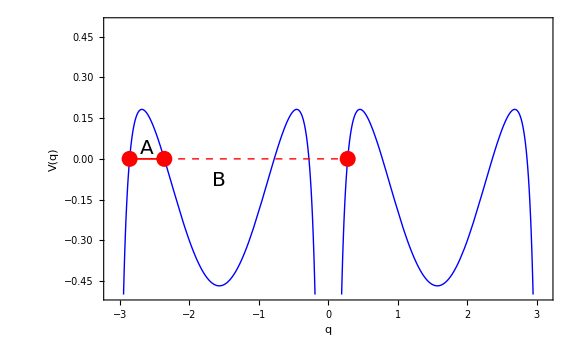

```mathematica
periodsPlot=Plot[U0[q,E0,mu],{q,-Pi+eps,Pi-eps},PlotStyle->Directive[Blue,Thick],Frame->True,Axes->False,FrameLabel->{"q","V(q)"},PlotRange->{-0.5,0.5},Epilog->{Red,PointSize[0.02],Point[{{q1,0},{q2,0},{q1+π,0}}],Red,Thick,Arrowheads[0.04],Arrow[{{q1,0},{q2,0}}],Arrow[{{q2,0},{q1,0}}],Black,Text[Style["A",20,Italic],{(q1+q2)/2,0.04}],Red,Dashed,Thick,Arrow[{{q2,0},{q1+π,0}}],Black,Text[Style["B",20,Italic],{(q2+q3)/2,-0.08}]},ImageSize->Large]
```

```mathematica
left1=rootsInInterval[U1,E0,mu,del,{-Pi+eps,-eps}];
right1=rootsInInterval[U1,E0,mu,del,{eps,Pi-eps}];


{q1,q2}=left1[[2;;3]];
q3=right1[[1]];
```

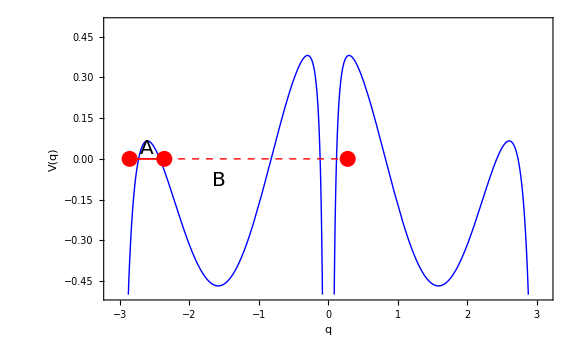

```mathematica
periodsPlot=Plot[U1[q,E0,mu,del],{q,-Pi+eps,Pi-eps},PlotStyle->Directive[Blue,Thick],Frame->True,Axes->False,FrameLabel->{"q","V(q)"},PlotRange->{-0.5,0.5},Epilog->{Red,PointSize[0.02],Point[{{q1,0},{q2,0},{q1+π,0}}],Red,Thick,Arrowheads[0.04],Arrow[{{q1,0},{q2,0}}],Arrow[{{q2,0},{q1,0}}],Black,Text[Style["A",20,Italic],{(q1+q2)/2,0.04}],Red,Dashed,Thick,Arrow[{{q2,0},{q1+π,0}}],Black,Text[Style["B",20,Italic],{(q2+q3)/2,-0.08}]},ImageSize->Large]
```

```mathematica
Clear[del,eps,E0, μ0, x1,x2,x3,x4,q1,q2,q3,q4,leftRoots, rightRoots, periodsPlot, U1, U0]
```

### Classical tilt term

```mathematica
ClearAll[V0,Vtilt,U0,Utilt,turningY,turningQ,critQ];

(*pure potentials*)
V0[q_,mu0_]:=Sin[q]^2+mu0 Sec[q]^2;
Vtilt[q_,mu0_,mu1_,mu2_]:=Sin[q]^2+(mu0+mu1 Sin[q]) Sec[q]^2 + mu2 Sin[q];

(*shifted by energy*)
U0[q_,E0_,mu0_]:=V0[q,mu0]-E0;
Utilt[q_,Es_,mu0_,mu1_,mu2_]:=Vtilt[q,mu0,mu1,mu2]-Es;
```

```mathematica
ClearAll[turningY,turningQ,critQ];

turningY[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=Module[{y,sol},sol=y/. NSolve[y^4-mu2 y^3+(Es-2) y^2+(mu1+mu2) y+(1+mu0-Es)==0,y,Reals];
Sort@Select[N[sol],-1<#<1&]];

turningQ[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=ArcSin/@turningY[Es,mu0,mu1,mu2];

critQ[mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=Module[{q,sol},sol=q/. Quiet@NSolve[{D[Vtilt[q,mu0,mu1,mu2],q]==0,-Pi/2<q<Pi/2},q,Reals];
Sort@N[sol]];
```

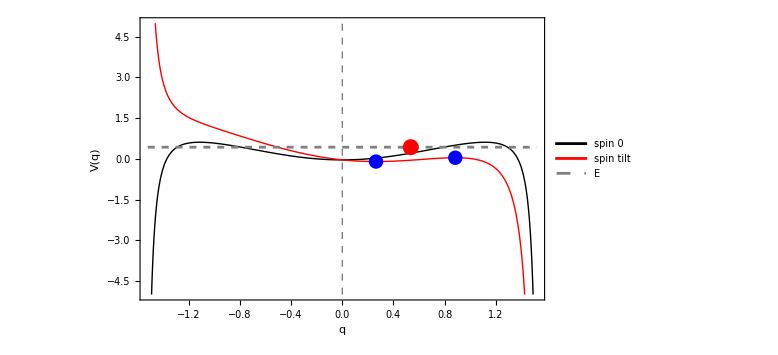

```mathematica
mu0= μ[2,10];
mu1=μ1[-2,2,10];
mu2=μ2[-2,2,10];
E0=Ε0[2,2,10];
Es=Εs[-2,2,2,10];
eps=0.05;

tp=turningQ[E0,mu0,mu1,mu2];
cp=critQ[mu0,mu1,mu2];

Plot[{V0[q,mu0],Vtilt[q,mu0,mu1,mu2],E0},{q,-Pi/2+eps,Pi/2-eps},PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Gray,Dashed]},PlotLegends->{"spin 0","spin tilt","E"},Frame->True,Axes->False,FrameLabel->{"q","V(q)"},PlotRange->{-5,5},Epilog->{Red,PointSize[0.02],Point[Transpose[{tp,ConstantArray[E0,Length[tp]]}]],Blue,PointSize[0.018],Point[Transpose[{cp,Vtilt[#,mu0,mu1,mu2]&/@cp}]],Dashed,Gray,Line[{{0,-5},{0,5}}]},ImageSize->Large]
```

```mathematica
mu2
```

-2/5

```mathematica
ClearAll[mu0,mu1,mu, E0, Es, V0, Vtilt, turningY,turningQ,critQ];
```

### Explorations of the “Quantum corrected” tilted potential effect

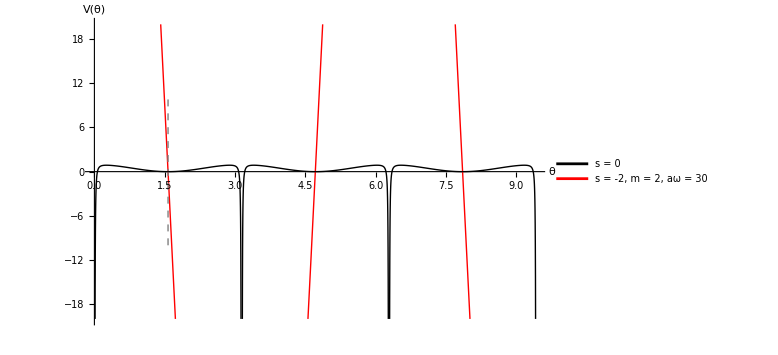

```mathematica
ClearAll[U0,Us,turningX,barrierX,eps,E0,Es, mu0,mu0s,ell,s,m,aw];

(*symmetric spin-0 model*)
V0[θ_,mu0_]:=Cos[θ]^2+mu0 Csc[θ]^2;

(*spin-tilted version:same base barrier,plus odd terms*)
Vs[θ_,mu0s_,s_,m_,aw_]:=Cos[θ]^2+mu0s Csc[θ]^2-2 m s Cos[θ] Csc[θ]^2 -2 aw s Cos[θ] ;

turningX[pot_,pars___]:=Module[{sol},sol=Quiet@NSolve[{pot[θ,pars]==0,0<θ<Pi},θ,Reals];
Sort@Cases[sol,Rule[θ,val_?NumericQ]:>N[val]]];

barrierX[pot_,pars___]:=Module[{sol},sol=Quiet@NSolve[{D[pot[θ,pars],θ]==0,0<θ<Pi},θ,Reals];
Sort@Cases[sol,Rule[θ,val_?NumericQ]:>N[val]]];

ell=2;
m=2;
s=-2;
aw=30;   

mu0s=μ0[s,m,aw];
mu0=μ[m,aw];

eps=0.01;
E0=Ε0[ell,m,aw];
Es=Εs[s,ell,m,aw];

tp0=turningX[V0,mu0];
bp0=barrierX[V0,mu0];

tps=turningX[Vs,mu0s,s,m,aw];
bps=barrierX[Vs,mu0s,s,m,aw];

Plot[Evaluate@{V0[θ,mu0],Vs[θ,mu0s,s,m,aw]},{θ,eps,3Pi-eps},PlotRange->{-20,20},PlotStyle->{Directive[Black,Thick],Directive[Red,Thick]},PlotLegends->{"s = 0",Row[{"s = ",s,", m = ",m,", aω = ",aw}]},AxesLabel->{"θ","V(θ)"},Epilog->{Black,PointSize[0.018],Point[Transpose[{tp0,V0[#,mu0]&/@tp0}]],Blue,PointSize[0.015],Point[Transpose[{bp0,V0[#,mu0]&/@bp0}]],Red,PointSize[0.018],Point[Transpose[{tps,Vs[#,mu0s,s,m,aw]&/@tps}]],Darker[Red],PointSize[0.015],Point[Transpose[{bps,Vs[#,mu0s,s,m,aw]&/@bps}]],Dashed,Gray,Line[{{Pi/2,-10},{Pi/2,10}}]},ImageSize->Large]
```

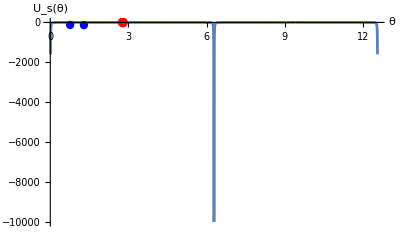

```mathematica
ClearAll[Us,turningThetaRaw,barrierThetaRaw,eps,K,m,s,c];

Us[th_,K_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=K-(m^2+s^2+2 m s Cos[th])/Sin[th]^2-c^2 Sin[th]^2-2 c s Cos[th];

turningThetaRaw[K_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=th/. Quiet@NSolve[{Us[th,K,m,s,c]==0,0<th<Pi},th,Reals];

barrierThetaRaw[K_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=th/. Quiet@NSolve[{D[Us[th,K,m,s,c],th]==0,0<th<Pi},th,Reals];

(*Example parameters*)
ClearAll[m,s,ell,c,mN,sN,cN,ellN,Kval]
mN=2;
sN=2;
ellN=2;
cN=10.0;          (*a ω large*)

Kval=Knumeric[sN,ellN,mN,cN];

eps=0.01;
tp=Sort@turningThetaRaw[Kval,mN,sN,cN];
bp=Sort@barrierThetaRaw[Kval,mN,sN,cN];

Plot[Us[th,Kval,mN,sN,cN]/cN^2,{th,eps,4Pi-eps},PlotRange->All,AxesLabel->{"θ","U_s(θ)"},Epilog->{Red,PointSize[0.018],Point[Transpose[{tp,Us[#,Kval,mN,sN,cN]&/@tp}]],Blue,PointSize[0.015],Point[Transpose[{bp,Us[#,Kval,mN,sN,cN]&/@bp}]]}]
```

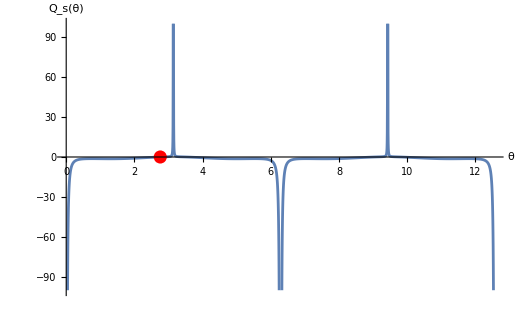

```mathematica
ClearAll[Qs,turningTheta,barrierTheta];

Qs[th_,K_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=Us[th,K,m,s,c]+1/4+1/(4 Sin[th]^2);

turningTheta[K_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=th/. Quiet@NSolve[{Qs[th,K,m,s,c]==0,0<th<Pi},th,Reals];

barrierTheta[K_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=th/. Quiet@NSolve[{D[Qs[th,K,m,s,c],th]==0,0<th<Pi},th,Reals];

tp=Sort@turningTheta[Kval,mN,sN,cN];
bp=Sort@barrierTheta[Kval,mN,sN,cN];

Plot[Qs[th,Kval,mN,sN,cN]/cN^2,{th,eps,4Pi-eps},PlotRange->{-100,100},AxesLabel->{"θ","Q_s(θ)"},Epilog->{Red,PointSize[0.018],Point[Transpose[{tp,Qs[#,Kval,mN,sN,cN]&/@tp}]],Blue,PointSize[0.015],Point[Transpose[{bp,Qs[#,Kval,mN,sN,cN]&/@bp}]]}]
```

```mathematica
Manipulate[Module[{tp=Sort@turningTheta[K,m,s,c]},Plot[Qs[th,K,m,s,c]/c^2,{th,eps,Pi-eps},PlotRange->{-10,10},Epilog->{Red,PointSize[0.017],Point[Transpose[{tp,Qs[#,K,m,s,c]&/@tp}]]}]],{{m,2},0,6,1},{{s,2},-2,2,1},{{c,10.},2.,30.},{{K,120.},0.,400.},TrackedSymbols:>{m,s,c,K}]
```

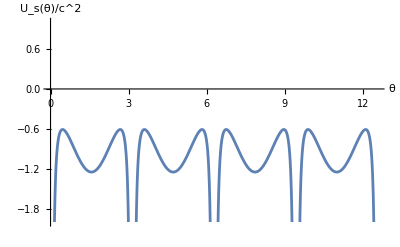

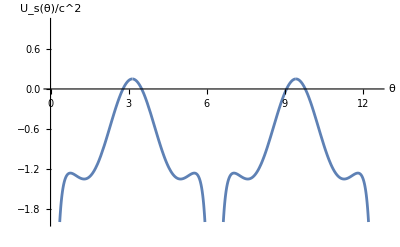

```mathematica
Uscaled[th_,Ks_?NumericQ,m_?NumericQ,s_?NumericQ,c_?NumericQ]:=Us[th,Ks,m,s,c]/c^2;

Plot[Uscaled[th,Kval,mN,0,cN],{th,eps,4 Pi-eps},PlotRange->{-2,1},AxesLabel->{"θ","U_s(θ)/c^2"}]
Plot[Uscaled[th,Kval,mN,2,cN],{th,eps,4 Pi-eps},PlotRange->{-2,1},AxesLabel->{"θ","U_s(θ)/c^2"}]
```

```mathematica
ClearAll[Us,Qs,m,ell,s,mN,ellN,sN, cN, barrierTheta,barrierThetaRaw, tp, bp, turningTheta, barrierThetaRaw, critQ, barrierX, E0, Es, Kval, eps, mu0, mu0s, tp0, bp0]
```

## Toric diagrams (for talks)

```mathematica
R=2.2;   (*major radius*)
r=0.8;   (*minor radius*)

torus[u_,v_]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};

torusSurf=ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},Mesh->None,PlotStyle->Directive[Opacity[0.45],LightGray],BoundaryStyle->None];

(*A-cycle:around the tube*)
Acycle=ParametricPlot3D[torus[0.9,v],{v,0,2 Pi},PlotStyle->{Thick,Red}];

(*B-cycle:around the hole*)
Bcycle=ParametricPlot3D[torus[u,0.2],{u,0,2 Pi},PlotStyle->{Thick,Blue}];

labels=Graphics3D[{Text[Style["A",20,Bold,Red],torus[0.9,Pi/2]+{0.15,0.15,0.15}],Text[Style["B",20,Bold,Blue],torus[Pi/2,0.2]+{0.15,0.15,0.15}]}];

Show[torusSurf,Acycle,Bcycle,labels,Boxed->False,Axes->False,Lighting->"Neutral",ViewPoint->{2.0,-2.3,1.6},ImageSize->600,Background->White]
```

-Graphics3D-

```mathematica
branchPts={-2.2,-1.1,0.4,1.3};

branchCutFig=Graphics[{Thick,Black,Line[{{-3,0},{2,0}}],Red,PointSize[0.02],Point[Transpose[{branchPts,{0,0,0,0}}]],Red,Thick,Line[{{branchPts[[1]],0},{branchPts[[2]],0}}],Blue,Thick,Line[{{branchPts[[2]],0.08},{branchPts[[4]],0.08}}],Text[Style["A",18,Bold,Red],{Mean[branchPts[[1;;2]]],-0.15}],Text[Style["B",18,Bold,Blue],{Mean[{branchPts[[2]],branchPts[[4]]}],0.22}]},PlotRange->{{-3,2},{-0.4,0.4}},ImageSize->400,Axes->False];
```

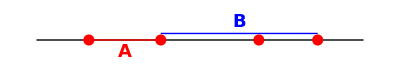

```mathematica
GraphicsRow[{branchCutFig,Show[torusSurf,Acycle,Bcycle,labels,Boxed->False,Axes->False,Lighting->"Neutral",ViewPoint->{2.0,-2.3,1.6},ImageSize->400]},Spacings->20]
```

```mathematica
arrowA=Graphics3D[{Red,Arrowheads[0.04],Arrow[{torus[0.9,1.2],torus[0.9,1.6]}]}];

arrowB=Graphics3D[{Blue,Arrowheads[0.04],Arrow[{torus[1.0,0.2],torus[1.35,0.2]}]}];

Show[torusSurf,Acycle,Bcycle,labels,arrowA,arrowB,Boxed->False,Axes->False,Lighting->"Neutral",ViewPoint->{2.0,-2.3,1.6},ImageSize->600]
```

-Graphics3D-

```mathematica
ClearAll[R,r, arrowA, arrowB, branchPts, branchCutFig, torus, labels, torusSurf,Acycle, Bcycle]
```

```mathematica
ClearAll["Global`*"];

(*---Torus as a visual model of the elliptic curve---*)
R=2.4;   (*major radius*)
r=0.8;   (*minor radius*)

torus[u_,v_]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};

tu[u_,v_]:=D[torus[uu,vv],uu]/. {uu->u,vv->v};
tv[u_,v_]:=D[torus[uu,vv],vv]/. {uu->u,vv->v};

surfNormal[u_,v_]:=Normalize[Cross[tu[u,v],tv[u,v]]];

(*---Choose an A-cycle gamma:fix v=v0 and let u run---*)
v0=0.7;

gamma[t_]:=torus[t,v0];
tgamma[t_]:=Normalize[D[gamma[τ],τ]/. τ->t];
ngamma[t_]:=surfNormal[t,v0];

(*second normal direction orthogonal to tangent*)
bgamma[t_]:=Normalize[Cross[tgamma[t],ngamma[t]]];

(*---Tube parameters---*)
delta=0.1;   (*offset off the surface,so the tube lies in the complement*)
rho=0.2;   (*radius of the Griffiths tube*)

tube[t_,phi_]:=gamma[t]+delta ngamma[t]+rho (Cos[phi] ngamma[t]+Sin[phi] bgamma[t]);

(*---Plots---*)
torusPlot=ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},Mesh->None,PlotStyle->Directive[Opacity[0.42],LightGray],BoundaryStyle->None,PlotPoints->60];

gammaPlot=ParametricPlot3D[gamma[t],{t,0,2 Pi},PlotStyle->Directive[Red,Thick],PlotPoints->200];

tubePlot=ParametricPlot3D[tube[t,phi],{t,0,2 Pi},{phi,0,2 Pi},Mesh->None,PlotStyle->Directive[Opacity[0.6],Orange],BoundaryStyle->None,PlotPoints->{120,24}];

label=Graphics3D[{Black,Text[Style["T(γ)",18,Bold,Blue],gamma[0.8]+{0.15,0.05,0.2}]}];

Show[torusPlot,tubePlot,gammaPlot,label,Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->Large]
```

-Graphics3D-

```mathematica
u0=1.0;

gamma[t_]:=torus[u0,t];
tgamma[t_]:=Normalize[D[gamma[τ],τ]/. τ->t];
ngamma[t_]:=surfNormal[u0,t];
bgamma[t_]:=Normalize[Cross[tgamma[t],ngamma[t]]];

(*---Plots---*)
torusPlot=ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},Mesh->None,PlotStyle->Directive[Opacity[0.22],LightGray],BoundaryStyle->None,PlotPoints->60];

gammaPlot=ParametricPlot3D[gamma[t],{t,0,2 Pi},PlotStyle->Directive[Red,Thick],PlotPoints->200];

tubePlot=ParametricPlot3D[tube[t,phi],{t,0,2 Pi},{phi,0,2 Pi},Mesh->None,PlotStyle->Directive[Opacity[0.7],Orange],BoundaryStyle->None,PlotPoints->{120,24}];

label=Graphics3D[{Black,Text[Style["T(γ)",18,Bold,Blue],gamma[0.8]+{0.15,0.05,0.2}]}];

Show[torusPlot,tubePlot,gammaPlot,label,Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->Large]
```

-Graphics3D-

```mathematica
(*---Torus embedding---*)
R=2.7;   (*major radius*)
r=1.0;   (*minor radius*)

torus[u_,v_]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};

(*---Pole locations in parameter space (u,v)---*)
poles={{1.0,1.0},{4.2,2.2}};

holeRadius=0.18;   (*size of deleted puncture neighborhood*)
cRadius=0.28;   (*radius of c-cycle drawn around each puncture*)

(*squared distance in parameter space to nearest pole*)
d2[u_,v_]:=Min@@(((u-#[[1]])^2+(v-#[[2]])^2)&/@poles);

(*---Torus with punctures---*)
torusPlot=ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},RegionFunction->Function[{x,y,z,u,v},d2[u,v]>holeRadius^2],Mesh->None,PlotStyle->Directive[Opacity[0.35],LightGray],BoundaryStyle->None,PlotPoints->100,MaxRecursion->2];

(*---c-cycles around each puncture---*)
cCycle[{u0_,v0_},color_]:=ParametricPlot3D[torus[u0+cRadius Cos[t],v0+cRadius Sin[t]],{t,0,2 Pi},PlotStyle->{color,Thick},PlotPoints->200];

c1Plot=cCycle[poles[[1]],Red];
c2Plot=cCycle[poles[[2]],Blue];

(*---labels---*)
label3D[text_,pt_,shift_,color_]:=Graphics3D[{Text[Style[text,18,Bold,color],torus@@pt+shift]}];

lab1=label3D["\!\(\*SubscriptBox[\(c\), \(+\)]\)",{poles[[1,1]]+cRadius,poles[[1,2]]},{0.2,0.1,0.15},Red];

lab2=label3D["\!\(\*SubscriptBox[\(c\), \(-\)]\)",{poles[[2,1]]+cRadius,poles[[2,2]]},{0.2,-0.1,0.15},Blue];

(*optional:mark the puncture centers*)
poleMarkers=Graphics3D[{Black,PointSize[0.02],Point[torus@@@poles]}];

Show[torusPlot,c1Plot,c2Plot,lab1,lab2,poleMarkers,Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->Large,ViewPoint->{2.2,-2.0,1.4}]
```

-Graphics3D-

```mathematica
(*---Torus embedding---*)
R=2.7;
r=1.0;

torus[u_,v_]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};

(*---Choose puncture locations in parameter space---*)
pPlus={0.95,1.0};
pMinus={4.1,2.25};
poles={pPlus,pMinus};

holeRadius=0.16;
cRadius=0.26;

d2[u_,v_]:=Min@@(((u-#[[1]])^2+(v-#[[2]])^2)&/@poles);

(*---Background torus with holes removed---*)
torusPlot=ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},RegionFunction->Function[{x,y,z,u,v},d2[u,v]>holeRadius^2],Mesh->None,PlotStyle->Directive[Opacity[0.22],LightGray],BoundaryStyle->None,PlotPoints->100,MaxRecursion->2];

(*---A-cycle:fix v=vA,go around u---*)
vA=0.55;
Aplot=ParametricPlot3D[torus[u,vA],{u,0,2 Pi},PlotStyle->{Red,Thick},PlotPoints->300];

(*---B-cycle:fix u=uB,go around v---*)
uB=2.25;
Bplot=ParametricPlot3D[torus[uB,v],{v,0,2 Pi},PlotStyle->{Blue,Thick},PlotPoints->300];

(*---Small c-cycles around punctures---*)
cCycle[{u0_,v0_},color_]:=ParametricPlot3D[torus[u0+cRadius Cos[t],v0+cRadius Sin[t]],{t,0,2 Pi},PlotStyle->{color,Thick},PlotPoints->250];

CplusPlot=cCycle[pPlus,Darker[Green]];
CminusPlot=cCycle[pMinus,Purple];

(*---Puncture markers---*)
poleMarkers=Graphics3D[{Black,PointSize[0.02],Point[torus@@pPlus],Point[torus@@pMinus]}];

(*---Labels---*)
label[text_,pos_,shift_,color_]:=Graphics3D[{Text[Style[text,18,Bold,color],torus@@pos+shift]}];

Alab=label["A",{1.2,vA},{0.15,0.1,0.15},Red];
Blab=label["B",{uB,1.0},{0.15,0.0,0.2},Blue];
Cplab=label[Subscript["C","+"],{pPlus[[1]]+cRadius,pPlus[[2]]},{0.15,0.12,0.15},Darker[Green]];
Cmlab=label[Subscript["C","-"],{pMinus[[1]]+cRadius,pMinus[[2]]},{0.15,-0.08,0.15},Purple];

Show[torusPlot,Aplot,Bplot,CplusPlot,CminusPlot,poleMarkers,Alab,Blab,Cplab,Cmlab,Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->Large,ViewPoint->{2.3,-2.1,1.5}]
```

-Graphics3D-

```mathematica
(*---Torus embedding---*)
R=2.7;
r=1.0;

torus[u_,v_]:={(R+r Cos[v]) Cos[u],(R+r Cos[v]) Sin[u],r Sin[v]};

(*---Choose puncture locations in parameter space---*)
pPlus={0.95,1.0};
pMinus={4.1,2.25};
poles={pPlus,pMinus};

holeRadius=0.16;
cRadius=0.26;

d2[u_,v_]:=Min@@(((u-#[[1]])^2+(v-#[[2]])^2)&/@poles);

(*---Background torus with holes removed---*)
torusPlot=ParametricPlot3D[torus[u,v],{u,0,2 Pi},{v,0,2 Pi},RegionFunction->Function[{x,y,z,u,v},d2[u,v]>holeRadius^2],Mesh->None,PlotStyle->Directive[Opacity[0.22],LightGray],BoundaryStyle->None,PlotPoints->100,MaxRecursion->2];

(*---A-cycle:fix v=vA,go around u---*)
vA=0.55;

(*---B-cycle:fix u=uB,go around v---*)
uB=2.25;


(*---Small c-cycles around punctures---*)
cCycle[{u0_,v0_},color_]:=ParametricPlot3D[torus[u0+cRadius Cos[t],v0+cRadius Sin[t]],{t,0,2 Pi},PlotStyle->{color,Thick},PlotPoints->250];

CplusPlot=cCycle[pPlus,Darker[Green]];
CminusPlot=cCycle[pMinus,Purple];

(*---Puncture markers---*)
poleMarkers=Graphics3D[{Black,PointSize[0.02],Point[torus@@pPlus],Point[torus@@pMinus]}];

(*---Labels---*)
label[text_,pos_,shift_,color_]:=Graphics3D[{Text[Style[text,18,Bold,color],torus@@pos+shift]}];


Cmlab=label["p_1",{pMinus[[1]]+cRadius,pMinus[[2]]},{0.45,-0.08,0.15},Purple];
Cplab=label["p_2",{pPlus[[1]]+cRadius,pPlus[[2]]},{0.15,0.12,0.15},Darker[Green]];

Show[torusPlot,CplusPlot,CminusPlot,poleMarkers,Cmlab,Cplab,Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->Large,ViewPoint->{2.3,-2.1,1.5}]
```

-Graphics3D-

```mathematica
Clear[r,R, d2, pPlus, pPlus, torus, Cmlab, pMinus,uB, CminusPlot, Cplab, CplusPlot, cCycle, label, poleMarkers, poles, torusPlot, vA, Aplot, Bplot]
```

## Period ratio tau

## Setup params

```mathematica
ClearAll[s,m,ell,μ0,μ1,μ2,E0,Es,E1]
μ0[s_,m_,c_]:=(1/4-(m^2+s^2))/c^2
μ1[s_,m_,c_]:=2m s/c^2
μ2[s_,m_,c_]:=2 s/c
setτParams[s_,ell_,m_,c_] := <| "Es"->Εs[s, ell,m,c], "μ0"->μ0[s,m,c], "μ1"->μ1[s,m,c] , "μ2"->μ2[s,m,c]|>
```

```mathematica
rootPrec=50;
```

```mathematica
τ0params = {};
Do[
ω=i; 
If[Mod[i,10]==0, AppendTo[τ0params,setτParams[0,2,2,N[ω,rootPrec]]], 1],
{i,1,1000}
]
```

$Aborted

```mathematica
τ2params = {};
Do[
ω=i; 
If[Mod[i,10]==0, AppendTo[τ2params,setτParams[-2,2,2,N[ω,rootPrec]]], 1],
{i,1,1000}
]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

SpinWeightedSpheroidalEigenvalue::findroot: FindRoot failed to converge to the requested accuracy.

General::stop: Further output of SpinWeightedSpheroidalEigenvalue::findroot will be suppressed during this calculation.

$Aborted

## Toy model

```mathematica
ClearAll[lambdaFromRoots,tauFromRoots];

(*Cross-ratio giving the Legendre parameter m=k^2*)
lambdaFromRoots[{e1_,e2_,e3_,e4_}]:=((e1-e2) (e3-e4))/((e1-e3) (e2-e4));

(*Period ratio tau=ω_B/ω_A in one standard convention*)
tauFromRoots[roots_List]:=Module[{lam},lam=lambdaFromRoots[roots];
I EllipticK[1-lam]/EllipticK[lam]];
```

```mathematica
ClearAll[quartic,rootsE,tauE];

(*Example placeholder:replace this with your actual quartic in X*)
quartic[X_,Ε_]:=(X-1) (X+1) (X-1/Sqrt[Ε+2]) (X+1/Sqrt[Ε+2]);

rootsE[Ε_?NumericQ]:=Module[{r},r=X/. NSolve[quartic[X,Ε]==0,X];
SortBy[r,{Re,Im}]];

tauE[Ε_?NumericQ]:=tauFromRoots[rootsE[Ε]];
```

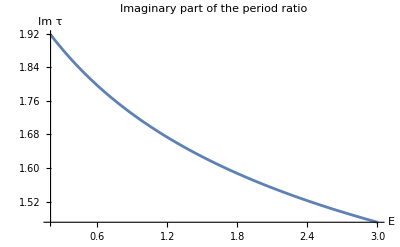

```mathematica
Plot[Im[tauE[Ε]],{Ε,0.2,3},AxesLabel->{"E","Im τ"},PlotLabel->"Imaginary part of the period ratio"]
```

```mathematica
Clear[tauE, rootsE, tauFromRoots,lambdaFromRoots, quartic ]
```

## Symmetric period ratio (τ torus modulus)

```mathematica
Clear[intSubs,N0A,N0B]
intSubs[Ε_,μ_]:= {k->Sqrt[a/b],a->1/2(Ε+1-Sqrt[(Ε-1)^2+4 μ]), b->1/2(Ε+1+Sqrt[(Ε-1)^2+4 μ])}

N0A[Ε0_,μ_]:=(4 √2 (k^2 (a-1) myEllipticK[k]+(a-1) (a-k^2) myEllipticPi[a,k]+a k myEllipticE[k]))/(k √a)//. Evaluate[intSubs[Ε0,μ]]
N0B[Ε0_,μ_]:=-1/2 N0A[Ε0,μ]+(2 Sqrt[2]/(k^2 Sqrt[a])((a-k^2)(a-1)myEllipticPi[b,1/k]+(a-k^2)myEllipticK[1/k] + a k^2 myEllipticE[1/k])//.Evaluate@intSubs[Ε0,μ])
```

```mathematica
N0A[Ε0[2,2,10.],μ[2,10.]]
N0B[Ε0[2,2,10.],μ[2,10.]]
```

0.444138

0.936429+0.467853 ⅈ

```mathematica
AcycleSym[l_,m_,c_]:=Module[{E0,k,mu,a,b},
E0=Ε0[l,m,c];
mu=μ[m,c];
a=1/2(E0+1-Sqrt[(E0-1)^2+4 mu]);
 b=1/2(E0+1+Sqrt[(E0-1)^2+4 mu]);
k=Sqrt[a/b];
<|"μ"->mu, "Ε"->E0,"val"-> (4Sqrt[2])/(k Sqrt[a])(k^2(a-1)myEllipticK[k]+(a-1)(a-k^2)myEllipticPi[a,k] + a k myEllipticE[k]), 
"series"-> (π Sqrt[2](E0-mu))/Sqrt[mu+1]+(π (1-2 mu)(E0-mu)^2)/(4 Sqrt[2] Sqrt[mu+1]^5) + (π (8(mu-3)+3)(E0-mu)^3)/(32  Sqrt[2](mu+1)^(9/2))+(π(25-10 mu(8 mu^2-60 mu+45))(E0-mu)^4)/(512 Sqrt[2](mu+1)^(13/2))|>
]

BcycleSym[l_,m_,c_]:=Module[{E0,k,mu,a,b},
E0=Ε0[l,m,c];
mu=μ[m,c];
a=1/2(E0+1-Sqrt[(E0-1)^2+4 mu]);
 b=1/2(E0+1+Sqrt[(E0-1)^2+4 mu]);
k=Sqrt[a/b];
<|"μ"->mu, "Ε"->E0,"val"->-(AcycleSym[l,m,c]["val"])/2+2 Sqrt[2]/(k^2 Sqrt[a])((a-k^2)(a-1)myEllipticPi[b,1/k]+(a-k^2)myEllipticK[1/k] + a k^2 myEllipticE[1/k]),
"series"->ⅈ 2 Sqrt[2](Sqrt[mu+1] + Sqrt[mu]ArcSinh[Sqrt[mu]] )+ π Sqrt[2 mu]  - (ⅈ (18 mu-5)(E0-mu)^2)/(16 Sqrt[2](mu+1)^(5/2))+
ⅈ *((48 mu^2-96 mu+9)(E0-mu)^3)/(64 Sqrt[2](mu+1)^(9/2))+ ⅈ/(2π)(1-Log[(E0-mu)/(16(mu+1)^2)])*
((π Sqrt[2](E0-mu))/Sqrt[mu+1]+(π (1-2 mu)(E0-mu)^2)/(4 Sqrt[2](mu+1)^(5/2)) + (π (8(mu-3)+3)(E0-mu)^3)/(32  Sqrt[2](mu+1)^(9/2))+(π(25-10 mu(8 mu^2-60 mu+45))(E0-mu)^4)/(512 Sqrt[2](mu+1)^(13/2))) |>
]
```

```mathematica
AcycleSym[2,2,10.]
BcycleSym[2,2,10.]
```

<|μ→-0.0375,Ε→0.430403,val→0.444138,series→2.09425|>

<|μ→-0.0375,Ε→0.430403,val→0.936429+0.467853 ⅈ,series→0.+5.09106 ⅈ|>

#### τ as elliptic modulus K(1-m)/K(m)

```mathematica
ClearAll[quartic, rootsE, tauE, tauFromRoots, lambdaFromRoots]
```

```mathematica
ClearAll[P4,tauFromRoots,tauEs];

P4[x_,E0_,μ0_,μ1_]:=-x^4+(2-E0) x^2-μ1 x+(E0-1-μ0);

tauFromRoots[roots_List]:=Module[{e1,e2,e3,e4,m,τ},{e1,e2,e3,e4}=roots;
m=((e2-e1) (e4-e3))/((e3-e1) (e4-e2));
τ=I EllipticK[1-m]/EllipticK[m];
If[Im[τ]<0,-τ,τ]];

tauEs[E0_?NumericQ,μ0_?NumericQ,μ1_?NumericQ]:=Module[{roots},roots=x/. NSolve[P4[x,E0,μ0,μ1]==0,x,WorkingPrecision->50];
roots=SortBy[roots,Re];(*okay only if you're in a regime where this is stable*)tauFromRoots[roots]];
```

```mathematica
taus[paramAssoc_]:=Module[{roots},roots=x/. NSolve[P4[x,paramAssoc["Es"],paramAssoc["μ0"],paramAssoc["μ1"]]==0,x,WorkingPrecision->WP];
roots=SortBy[roots,Re];(*okay only if you're in a regime where this is stable*)
tauFromRoots[roots]];
```

```mathematica
tau0List=Map[taus,τ0params];
```

#### Integrate symmetric periods numerically and compute tau from the numerical data

```mathematica
ClearAll[P4sym,rootsSym,πA,πB,τsym];

P4sym[x_,Es_,μ0_]:=-x^4+(2-Es) x^2+(Es-1-μ0);
rootsSym[Es_?NumericQ,μ0_?NumericQ]:=Module[{r},r=x/. NSolve[P4sym[x,Es,μ0]==0,x,WorkingPrecision->48];
Sort[Chop[r]]];

πA[Es_?NumericQ,μ0_?NumericQ]:=Module[{e1,e2,e3,e4},{e1,e2,e3,e4}=rootsSym[Es,μ0];
2 NIntegrate[1/Sqrt[Abs[P4sym[x,Es,μ0]]],{x,e1,e2},WorkingPrecision->WP,AccuracyGoal->20,PrecisionGoal->20]];

πB[Es_?NumericQ,μ0_?NumericQ]:=Module[{e1,e2,e3,e4},{e1,e2,e3,e4}=rootsSym[Es,μ0];
2 I NIntegrate[1/Sqrt[Abs[P4sym[x,Es,μ0]]],{x,e2,e3},WorkingPrecision->WP,AccuracyGoal->20,PrecisionGoal->20]];

τsym[paramAssoc_]:= Module[{Es= paramAssoc["Es"], μ0=paramAssoc["μ0"]},
πB[Es,μ0]/πA[Es,μ0]]
```

```mathematica
τ0List=Map[τsym,τ0params];
```

NSolve::precw: The precision of the argument function ({-0.006967952106026572135107990082540441708368680701+1.006973022414301315239488736431918483893333526563 x^2-x^4}) is less than WorkingPrecision (48).

NSolve::precw: The precision of the argument function ({-0.00688796063921990655367527821999841045712775796+1.006892915058561959665050625029352354174924032237 x^2-x^4}) is less than WorkingPrecision (48).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

```mathematica
(* remove the funny negative energy value that we know is a fluke *)
badPos=First@FirstPosition[τ0params[[All,"Es"]],_?Negative]
```

6

```mathematica
assocListClean=Delete[τ0params,badPos];
τ0ListClean=Delete[τ0List,badPos];
tau0ListClean=Delete[tau0List,badPos];
```

```mathematica
Length[τ0ListClean]==Length@tau0ListClean==Length@assocListClean
```

True

```mathematica
Evals = assocListClean[[All,"Es"]];
(* elliptic K ratio data *)
dataKratio=Transpose[{Evals,-ⅈ tau0ListClean}];
dataNumericPeriodRatio=Transpose[{Evals,-ⅈ τ0ListClean}];
```

```mathematica
diffs=Transpose[{Evals,Abs[dataNumericPeriodRatio[[All,2]]-dataKratio[[All,2]]]}];
```

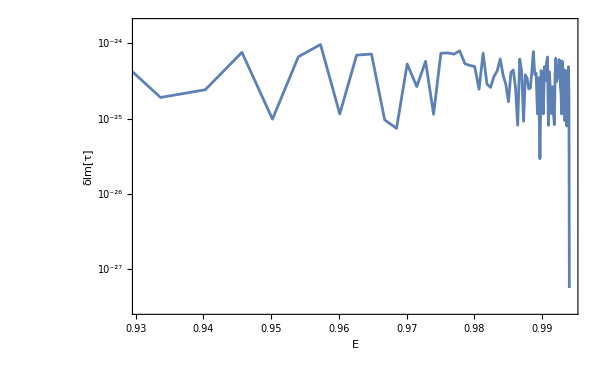

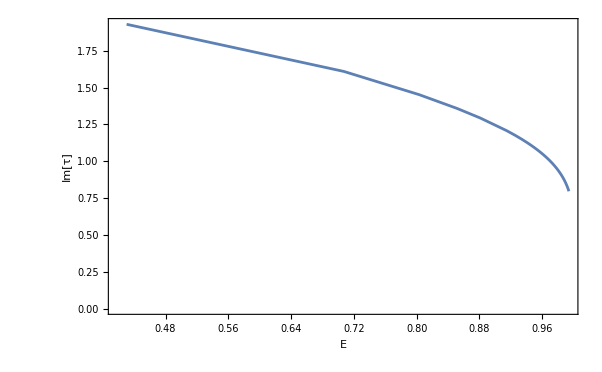

```mathematica
ListLogPlot[diffs, PlotRange->Automatic,Joined->True,Frame->True,FrameLabel->{"E","δIm[τ]"}]
ListPlot[{dataKratio}, PlotRange->All,Joined->True,Frame->True,FrameLabel->{"E","Im[τ]"}]
```

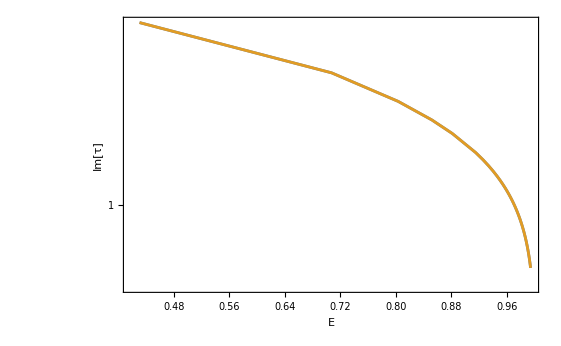

```mathematica
tau0List[[1;;10]]
```

{1.92993146859009652202998913004 ⅈ,1.61004193614332163050950924051 ⅈ,1.45247479784850021609378952237 ⅈ,1.35833210070303692046384765018 ⅈ,1.29367975263848802651423337236 ⅈ,3.5094407795555699253781807611 ⅈ,1.20760004216561036472571383426 ⅈ,1.17668969016693903139789480795 ⅈ,1.15077183866412747578702990862 ⅈ,1.12857998836046822152984475569 ⅈ}

```mathematica
τ0List[[1;;10]]
```

{1.929931468590096522029990915366 ⅈ,1.610041936143321630509508483766 ⅈ,1.452474797848500216093789839076 ⅈ,1.35833210070303692046384842386 ⅈ,1.293679752638488026514233250655 ⅈ,3.509440779555569925378193477501 ⅈ,1.207600042165610364725712771768 ⅈ,1.176689690166939031397895719873 ⅈ,1.15077183866412747578703009925 ⅈ,1.128579988360468221529844514116 ⅈ}

```mathematica
Clear[diffs, assocListClean, badPos, πA, πB, dataKratio, dataNumericPeriodRatio, τsym, P4sym,τ0List, tau0List ]
```

## Asymmetric spin-2 period ratio (τ torus modulus)

#### generate parameter data

```mathematica
τ2params[[1]]
```

<|Es→1.166752528217016850222571060655678265604318484103,μ0→-0.0775,μ1→-0.08|>

```mathematica
E2vals = τ2params[[All,"Es"]];
μ0vals= τ2params[[All,"μ0"]];
μ1vals= τ2params[[All,"μ1"]];
μ2vals= τ2params[[All,"μ2"]];
```

```mathematica
ClearAll[P4,quarticRoots,bestRootMatch,minRootDistance,mFromRoots,tauStdFromRoots,tauPhysicalFromRoots,nearestTauShift,buildRootGrid,buildTauGrid,tauDataIm,tauDataRe];

(*---quartic---*)
P4[x_,Es_,mu0_,mu1_,mu2_]:=-x^4+mu2 x^3+(2-Es) x^2-(mu1+mu2) x+(Es-1-mu0);
(*P4[x_,Es_,mu0_,mu1_,mu2_]:=-x^4+(2-Es) x^2-mu1 x+(Es-1-mu0); *)
(* --- numerical roots --- *)
quarticRoots[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:rootPrec]:=Module[{x,es,m0,m1,m2,roots},{es,m0,m1,m2}=SetPrecision[{Es,mu0,mu1,mu2},wp];
roots=NSolveValues[P4[x,es,m0,m1,m2]==0,x,WorkingPrecision->wp];
Chop[N[roots,wp],10^(-wp/2)]];

(*---match new roots to previous labeling by minimizing total motion---*)
bestRootMatch[prev_List,new_List]/;Length[prev]==Length[new]:=First@MinimalBy[Permutations[new],Total[Abs[#-prev]]&];

(*---numerical roots at high precision---*)
ClearAll[trackRoots1D];

trackRoots1D[paramVals_List,mu0Fun_,mu1Fun_,mu2Fun_,EsFun_,wp_:rootPrec]:=Module[{rawRoots,tracked},rawRoots=Table[quarticRoots[EsFun[p],mu0Fun[p],mu1Fun[p],mu2Fun[p],wp],{p,paramVals}];
tracked=ConstantArray[{},Length[paramVals]];
tracked[[1]]=SortBy[rawRoots[[1]],{Re[#],Im[#]}&];
Do[tracked[[k]]=bestRootMatch[tracked[[k-1]],rawRoots[[k]]],{k,2,Length[paramVals]}];
tracked];

quarticRootsDebug[Es_,mu0_,mu1_,mu2_,wp_:rootPrec]:=Module[{x,es,m0,m1,m2,poly,roots},{es,m0,m1,m2}=SetPrecision[{Es,mu0,mu1,mu2},wp];
poly=P4[x,es,m0,m1,m2];
Print["poly = ",poly];
roots=NSolveValues[poly==0,x,WorkingPrecision->wp];
Print["roots = ",roots];
roots];

rootsSym[Es_?NumericQ,μ0_?NumericQ]:=Module[{r},r=x/. NSolve[P4sym[x,Es,μ0]==0,x,WorkingPrecision->48];
Sort[Chop[r]]];

(*---distance to nearest root collision---*)
minRootDistance[roots_List]:=Min[Abs/@(Subtract@@@Subsets[roots,{2}])];

(*---cross-ratio parameter m from an ordered root list {e1,e2,e3,e4}---*)
mFromRoots[{e1_,e2_,e3_,e4_}]:=((e2-e1) (e4-e3))/((e3-e1) (e4-e2));

(*---standard tau from the ordered roots---*)
tauStdFromRoots[roots_List]:=Module[{m,tau},
m=mFromRoots[roots];
tau=I EllipticK[1-m]/EllipticK[m];
If[Im[tau]<0,-tau,tau]];


(*---choose physical convention once and for all from symmetric calibration---*)
tauPhysicalFromRoots[roots_List,convention_:1]:=Module[{tau=tauStdFromRoots[roots]},Which[convention===1,tau,convention===-1,-1/tau,True,tau]];

(*---unwrap by integer shifts to keep continuity in the upper half-plane---*)
nearestTauShift[tau_,tauRef_,nmax_:3]:=First@MinimalBy[Select[Table[tau+n,{n,-nmax,nmax}],Im[#]>0&],Abs[#-tauRef]&];

Clear[unwrapTauByIntegerShift];

(*optional:remove jumps tau->tau+n coming from branch choices*)
unwrapTauByIntegerShift[tauList_List,nmax_:4]:=Module[{out=tauList,cands},Do[cands=Select[Table[tauList[[k]]+n,{n,-nmax,nmax}],Im[#]>0&];
out[[k]]=First@MinimalBy[cands,Abs[#-out[[k-1]]]&],{k,2,Length[tauList]}];
out];
```

```mathematica
plist=N@Subdivide[0,0.05,10];
rootsTrackedTest=trackRoots1D[plist,Function[p,0.02],Function[p,p],Function[p,0.8], Function[p,0.3],48];
Clear[plist, rootsTrackedTest, quarticRootsDebug]
```

```mathematica
Clear[getRoots]
getRoots[paramAssoc_?AssociationQ,wp_:rootPrec]:=Module[{Es,mu0,mu1,mu2},Es=N@SetPrecision[paramAssoc["Es"],wp];
mu0=N@SetPrecision[paramAssoc["μ0"],wp];
mu1=N@SetPrecision[paramAssoc["μ1"],wp];
mu2=N@SetPrecision[paramAssoc["μ2"],wp];
quarticRoots[Es,mu0,mu1,mu2,wp]];
```

```mathematica
mu0Fix=μ0vals[[10]]

tauConvention=1;   (*change to-1 if your physical tau is-1/tau_std*)
```

-0.000775

```mathematica
(* get the tracked roots *)
rootsTracked=Map[getRoots,τ2params]; //Quiet
```

```mathematica
rootsTracked[[1]]
```

{-0.99844463913549272481536224111215972048850966294902,-0.2242042405350100688942692476780974561801763684262-0.42827169652232279052781603534813430403580620972413 ⅈ,-0.2242042405350100688942692476780974561801763684262+0.42827169652232279052781603534813430403580620972413 ⅈ,1.046853120205512840399440243965223824376229037985}

```mathematica
tauConvention=1;   (*or-1*)
tauListRaw=tauPhysicalFromRoots[#,tauConvention]&/@rootsTracked;
tauList=unwrapTauByIntegerShift[tauListRaw];
```

```mathematica
tauList[[1]]
```

-0.65508163663741200439260919483436556457700856203+0.93863268780459255594007238633980743056586835886 ⅈ

```mathematica
badPos=First@FirstPosition[τ2params[[All,"Es"]],_?Negative]
```

6

```mathematica
assocListClean=Delete[τ2params,badPos];
```

```mathematica
tauListClean=Delete[tauList,badPos];
```

```mathematica
E2vals = assocListClean[[All,"Es"]];
```

```mathematica
data2=Transpose[{E2vals, Im[ tauListClean]}];
```

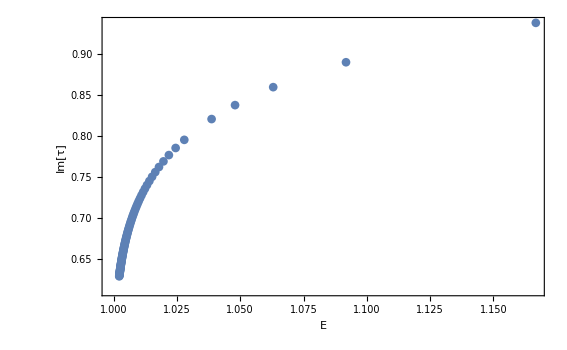

```mathematica
ListPlot[data2, PlotRange->All,Frame->True,FrameLabel->{"E","Im[τ]"}]
```

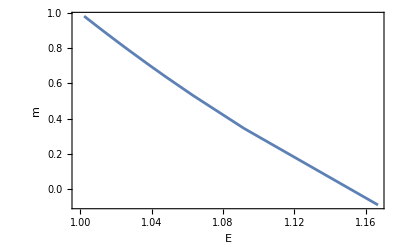

```mathematica
mCrossRatioList=Delete[mFromRoots/@rootsTracked,badPos]; (* compute the modulus *)


ListLinePlot[Transpose[{E2vals,mCrossRatioList}//Re],Frame->True,FrameLabel->{"E","m"},PlotRange->All]
```

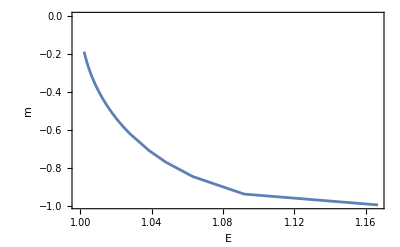

```mathematica
ListLinePlot[Transpose[{E2vals,Im@mCrossRatioList}],Frame->True,FrameLabel->{"E","m"},PlotRange->All]
```

```mathematica
ClearAll[P4,rootsRealOrdered,piAspin,piBspin,tauSpin];

P4[x_,Es_,μ0_,μ1_,μ2_]:=-x^4+μ2 x^3+(2-Es) x^2-(μ2+μ1) x+(Es-1-μ0);

rootsRealOrdered[paramAssoc_,wp_:48]:=Module[{Es,μ0,μ1,r,tol},Es=SetPrecision[paramAssoc["Es"],wp];
μ0=SetPrecision[paramAssoc["μ0"],wp];
μ1=SetPrecision[paramAssoc["μ1"],wp];
r=quarticRoots[Es,μ0,μ1,wp];
tol=10^(-wp/3);
If[Max[Abs[Im[r]]]>tol,Print["Warning: roots are not all real at this parameter point."]];
SortBy[Chop[r,tol],Re]];
```

```mathematica
piAspin[paramAssoc_,wp_:48]:=Module[{Es,μ0,μ1,μ2,e1,e2,e3,e4,mid,rad},Es=SetPrecision[paramAssoc["Es"],wp];
μ0=SetPrecision[paramAssoc["μ0"],wp];
μ1=SetPrecision[paramAssoc["μ1"],wp];
μ2=SetPrecision[paramAssoc["μ2"],wp];
{e1,e2,e3,e4}=rootsRealOrdered[paramAssoc,wp];
mid=(e1+e2)/2;
rad=(e2-e1)/2;
2 rad NIntegrate[Sin[θ]/Sqrt[P4[mid+rad Cos[θ],Es,μ0,μ1,μ2]],{θ,0,Pi},WorkingPrecision->wp,AccuracyGoal->20,PrecisionGoal->20,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

```mathematica
piBspin[paramAssoc_,wp_:48]:=Module[{Es,μ0,μ1,μ2,e1,e2,e3,e4,mid,rad},Es=SetPrecision[paramAssoc["Es"],wp];
μ0=SetPrecision[paramAssoc["μ0"],wp];
μ1=SetPrecision[paramAssoc["μ1"],wp];
μ2=SetPrecision[paramAssoc["μ2"],wp];
{e1,e2,e3,e4}=rootsRealOrdered[paramAssoc,wp];
mid=(e2+e3)/2;
rad=(e3-e2)/2;
2 I rad NIntegrate[Sin[θ]/Sqrt[-P4[mid+rad Cos[θ],Es,μ0,μ1,μ2]],{θ,0,Pi},WorkingPrecision->wp,AccuracyGoal->20,PrecisionGoal->20,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

```mathematica
tauSpin[paramAssoc_,wp_:WP]:=piBspin[paramAssoc,wp]/piAspin[paramAssoc,wp];
```

```mathematica
tauSpin[τ2params[[4]]]
```

NSolveValues::precw: The precision of the argument function ({0.0528007835845255634170451900947071822367058502909-63.995 x$90453+0.9520429664154744365829548099052928177632941497091 x$90453^2+64. x$90453^3-x$90453^4}) is less than WorkingPrecision (50).

NIntegrate::precw: The precision of the argument function (Sin[θ]/(√(-0.052800783584525563417045190094707182236705850290893204269788491-0.105 («83»+«97» Cos[θ])-«98» («83»+«1»)^2+«83» («1»)^3+(«83»+«97» Cos[θ])^4))) is less than WorkingPrecision (64.).

NSolveValues::precw: The precision of the argument function ({0.0528007835845255634170451900947071822367058502909-63.995 x$90497+0.9520429664154744365829548099052928177632941497091 x$90497^2+64. x$90497^3-x$90497^4}) is less than WorkingPrecision (50).

NIntegrate::precw: The precision of the argument function (Sin[θ]/(√(0.052800783584525563417045190094707182236705850290893204269788491+0.105 (-«97»+«81» Cos[θ])+«98» («1»)^2-«83» (-«97»+«1»)^3-(-«97»+«81» Cos[«1»])^4))) is less than WorkingPrecision (64.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.12321044320134004910485546543365836397582693989566103958035101174662498497441269721721520121214052661573619274276}. NIntegrate obtained 6.16210776098292533523493535900390928028589408517933247749596505219755755048328774266259285418313879888237241186181-0.0246402586649012034454402954706810423508616410846975734424762458608534729640341905146477400387654694266282863265236 ⅈ and 0.00233195705088715230420165306041236868463836795865881122264597854936056931198311290830111000768871400557166277442683 for the integral and error estimates.

0.8270847612079378735702008091131327763763281434416+0.003307242139288856227795021708193454829939956904153 ⅈ

```mathematica
ClearAll[trackedSqrtValues,complexCutPeriod];

trackedSqrtValues[vals_List]:=Module[{out,cand},out={Sqrt[vals[[1]]]};
Do[cand=Sqrt[vals[[k]]];
AppendTo[out,If[Abs[cand-out[[-1]]]<=Abs[-cand-out[[-1]]],cand,-cand]],{k,2,Length[vals]}];
out];

complexCutPeriod[roots_List,{i_,j_},n_:1200]:=Module[{a,b,others,c,d,θgrid,zvals,gvals,svals,fvals,dθ},{a,b}=roots[[{i,j}]];
others=roots[[Complement[Range[4],{i,j}]]];
{c,d}=others;
θgrid=N@Subdivide[0,Pi,n];
zvals=(a+b)/2+(a-b)/2 Cos[θgrid];
gvals=(zvals-c) (zvals-d);
svals=trackedSqrtValues[gvals];
(*factor 2=full cycle*)fvals=2/svals;
dθ=Differences[θgrid];
Total[(Most[fvals]+Rest[fvals]) dθ/2]];
```

```mathematica
piAspin[paramAssoc_,roots_List,wp_:80]:=complexCutPeriod[roots,{1,2},wp];

piBspin[paramAssoc_,roots_List,wp_:80]:=complexCutPeriod[roots,{2,3},wp];
```

```mathematica
tauSpin[paramAssoc_,roots_List,wp_:80]:=Module[{τ},τ=piBspin[paramAssoc,roots,wp]/piAspin[paramAssoc,roots,wp];
If[Im[τ]<0,-τ,τ]];
```

```mathematica
piAspin[τ2params[[2]],rootsTracked[[2]],80]
```

5.00703-3.06415 ⅈ

```mathematica
tauListNum=MapThread[tauSpin[#1,#2,80]&,{τ2params,rootsTracked}];
```

```mathematica
tauListNum[[1;;10]]
```

{-0.655082+0.938633 ⅈ,-0.544933+0.890457 ⅈ,-0.489719+0.860008 ⅈ,-0.454382+0.838034 ⅈ,-0.429065+0.820995 ⅈ,0.+3.24688 ⅈ,-0.394142+0.795572 ⅈ,-0.381301+0.785628 ⅈ,-0.370427+0.776941 ⅈ,-0.361047+0.769246 ⅈ}

```mathematica
tauList[[1;;10]]
```

{-0.65508163663741200439260919483436556457700856203+0.93863268780459255594007238633980743056586835886 ⅈ,-0.54493317791343157603153034395747659004726375915+0.89045729119145937892830897435741981914224835585 ⅈ,-0.48971943460534429765538000493373090524463884886+0.86000799099805491592139988712580222283732309346 ⅈ,-0.45438189056083982788507240771047655306978819746+0.83803393645605822416493798900623805862301033451 ⅈ,-0.42906514158830931287307772961542625481743489216+0.82099536384222213696699591547973270136390278812 ⅈ,3.2468753636992149107139512233398682656518263068 ⅈ,-0.39414151996623836486910144349033220672801063308+0.79557243678447033922755516249635987599398756363 ⅈ,-0.38130055445551871039009777897059257448342385443+0.7856277719651663582695146890493368215014391246 ⅈ,-0.37042704796572152081780506567651878929721433856+0.77694137363564574771150039399323058231687725787 ⅈ,-0.36104672198483350260389346118322842610414177674+0.76924554500736196954229634435697077549914833321 ⅈ}

```mathematica
ClearAll[reduceTau];

reduceTau[tau_]:=Module[{z=tau},(*shift into strip*)z=z-Round[Re[z]];
(*invert until|z| >=1*)While[Abs[z]<1,z=-1/z;
z=z-Round[Re[z]];];
(*final strip adjustment*)z=z-Round[Re[z]];
z];
```

```mathematica
tauFD=reduceTau/@tauListNum;
```

```mathematica
tauFD
```

{0.344918+0.938633 ⅈ,0.455067+0.890457 ⅈ,0.5+0.878062 ⅈ,0.5+0.922169 ⅈ,0.5+0.956726 ⅈ,0.+3.24688 ⅈ,0.5+1.00925 ⅈ,0.5+1.03019 ⅈ,-0.5+1.04871 ⅈ,0.5+1.0653 ⅈ,0.5+1.08032 ⅈ,0.5+1.09405 ⅈ,0.5+1.1067 ⅈ,0.5+1.11841 ⅈ,0.5+1.12932 ⅈ,0.5+1.13953 ⅈ,0.5+1.14912 ⅈ,0.5+1.15817 ⅈ,0.5+1.16673 ⅈ,0.5+1.17486 ⅈ,0.5+1.18259 ⅈ,-0.5+1.18997 ⅈ,0.5+1.19701 ⅈ,-0.5+1.20376 ⅈ,0.5+1.21024 ⅈ,0.5+1.21646 ⅈ,0.5+1.22244 ⅈ,-0.5+1.22821 ⅈ,0.5+1.23378 ⅈ,0.5+1.23916 ⅈ,0.5+1.24437 ⅈ,0.5+1.24941 ⅈ,0.5+1.25429 ⅈ,0.5+1.25903 ⅈ,-0.5+1.26363 ⅈ,-0.5+1.26811 ⅈ,-0.5+1.27246 ⅈ,0.5+1.27669 ⅈ,0.5+1.28082 ⅈ,0.5+1.28484 ⅈ,0.5+1.28876 ⅈ,0.5+1.29259 ⅈ,0.5+1.29633 ⅈ,0.5+1.29998 ⅈ,0.5+1.30355 ⅈ,0.5+1.30704 ⅈ,0.5+1.31046 ⅈ,-0.5+1.3138 ⅈ,0.5+1.31708 ⅈ,0.5+1.32029 ⅈ,-0.5+1.32343 ⅈ,0.5+1.32652 ⅈ,0.5+1.32955 ⅈ,0.5+1.33252 ⅈ,0.5+1.33543 ⅈ,0.5+1.3383 ⅈ,-0.5+1.34111 ⅈ,0.5+1.34387 ⅈ,0.5+1.34659 ⅈ,0.5+1.34926 ⅈ,0.5+1.35189 ⅈ,-0.5+1.35447 ⅈ,-0.5+1.35702 ⅈ,0.5+1.35952 ⅈ,0.5+1.36198 ⅈ,-0.5+1.36441 ⅈ,0.5+1.3668 ⅈ,-0.5+1.36916 ⅈ,0.5+1.37148 ⅈ,0.5+1.37377 ⅈ,0.5+1.37602 ⅈ,-0.5+1.37824 ⅈ,0.5+1.38044 ⅈ,-0.5+1.3826 ⅈ,0.5+1.38473 ⅈ,0.5+1.38684 ⅈ,0.5+1.38892 ⅈ,-0.5+1.39097 ⅈ,0.5+1.393 ⅈ,0.5+1.395 ⅈ,0.5+1.39697 ⅈ,0.5+1.39892 ⅈ,-0.5+1.40085 ⅈ,0.5+1.40275 ⅈ,0.5+1.40463 ⅈ,0.5+1.40649 ⅈ,0.5+1.40833 ⅈ,0.5+1.41015 ⅈ,0.5+1.41195 ⅈ,0.5+1.41372 ⅈ}

```mathematica
tauFDCleaned=Delete[tauFD, badPos];
```

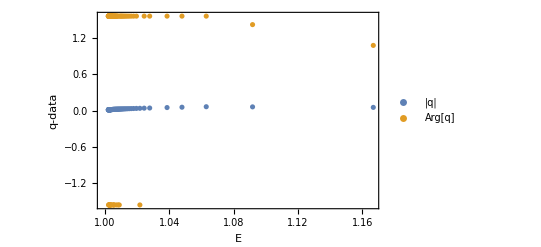

```mathematica
qList = Exp[I Pi #] & /@ tauFDCleaned;

ListPlot[
  {
    Transpose[{E2vals, Abs[qList]}],
    Transpose[{E2vals, Arg[qList]}]
  },
  Frame -> True, PlotRange->All,
  FrameLabel -> {"E", "q-data"},
  PlotLegends -> {"|q|", "Arg[q]"}
]
```

```mathematica
tau0FDCleaned = reduceTau/@tau0ListClean;
```

```mathematica
ClearAll[plotFundamentalDomainColored];

plotFundamentalDomainColoredOld[tauList_,paramVals_]:=Module[{pts,colors,arc,leftWall,rightWall,pmin,pmax},pts=Transpose[{Re[tauList],Im[tauList]}];
pmin=Min[paramVals];
pmax=Max[paramVals];
colors=ColorData["SolarColors"]/@Rescale[paramVals,{pmin,pmax}];
arc=Table[{Cos[t],Sin[t]},{t,Pi/3,2 Pi/3,0.002}];
leftWall={{-1/2,Sqrt[3]/2},{-1/2,2.2}};
rightWall={{1/2,Sqrt[3]/2},{1/2,2.2}};
Show[Graphics[{Thick,Black,Line[arc],Line[leftWall],Line[rightWall],Gray,Dashed,Line[{{-1,0},{1,0}}],MapThread[{#2,PointSize[0.017],Point[#1]}&,{pts,colors}]}],Frame->True,FrameLabel->{"Re[τ]","Im[τ]"},PlotRange->{{-0.7,0.7},{0,2.2}},AspectRatio->1.2,ImageSize->Large]];

ClearAll[plotFundamentalDomainColored];

plotFundamentalDomainColored[tauList_,paramVals_,paramLabel_:"E"]:=Module[{pts,arc,leftWall,rightWall,cf,pmin,pmax,colors},
pts=Transpose[{Re[tauList],Im[tauList]}];
pmin=Min[paramVals];
pmax=Max[paramVals];
cf=ColorData["SolarColors"];
colors=cf/@Rescale[paramVals,{pmin,pmax}];
arc=Table[{Cos[t],Sin[t]},{t,Pi/3,2 Pi/3,0.002}];
leftWall={{-1/2,Sqrt[3]/2},{-1/2,2.2}};
rightWall={{1/2,Sqrt[3]/2},{1/2,2.2}};
Legended[Show[Graphics[{Thick,Black,Line[arc],Line[leftWall],Line[rightWall],MapThread[{#2,PointSize[0.2],Point[#1]}&,{pts,colors}]}],Frame->True,FrameLabel->{"Re[τ]","Im[τ]"},PlotRange->{{-0.7,0.7},{0.5,1.5}},AspectRatio->1.2,ImageSize->Large],BarLegend[{cf,{pmin,pmax}},LegendLabel->paramLabel]]];

plotFundamentalDomainColored[tauList_,paramVals_,paramLabel_:"E"]:=Module[{pts,arc,leftWall,rightWall,cf,pmin,pmax,colors,ymax},pts=Transpose[{Re[tauList],Im[tauList]}];
pmin=Min[paramVals];
pmax=Max[paramVals];
ymax=Max[2.2,1.05 Max[Im[tauList]]];
cf=ColorData["SolarColors"];
colors=cf/@Rescale[paramVals,{pmin,pmax}];
arc=Table[{Cos[t],Sin[t]},{t,Pi/3,2 Pi/3,0.002}];
leftWall={{-1/2,Sqrt[3]/2},{-1/2,ymax}};
rightWall={{1/2,Sqrt[3]/2},{1/2,ymax}};
Legended[Show[Graphics[{Thick,Black,Line[arc],Line[leftWall],Line[rightWall],MapThread[{Opacity[0.7],#2,PointSize[0.013],Point[#1]}&,{pts,colors}]}],Frame->True,FrameLabel->{"Re[τ]","Im[τ]"},PlotRange->{{-0.7,0.7},{0.8,1.6}},AspectRatio->1.2,ImageSize->Large],BarLegend[{cf,{pmin,pmax}},LegendLabel->paramLabel]]];
```

```mathematica
plot1=plotFundamentalDomainColored[tau0FDCleaned,E2vals]
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 2 and 89.

-Graphics-

```mathematica
Export["symmetricTau.pdf",plot1]
```

symmetricTau.pdf

```mathematica
Max@E2vals
```

1.166752528217016850222571060655678265604318484103

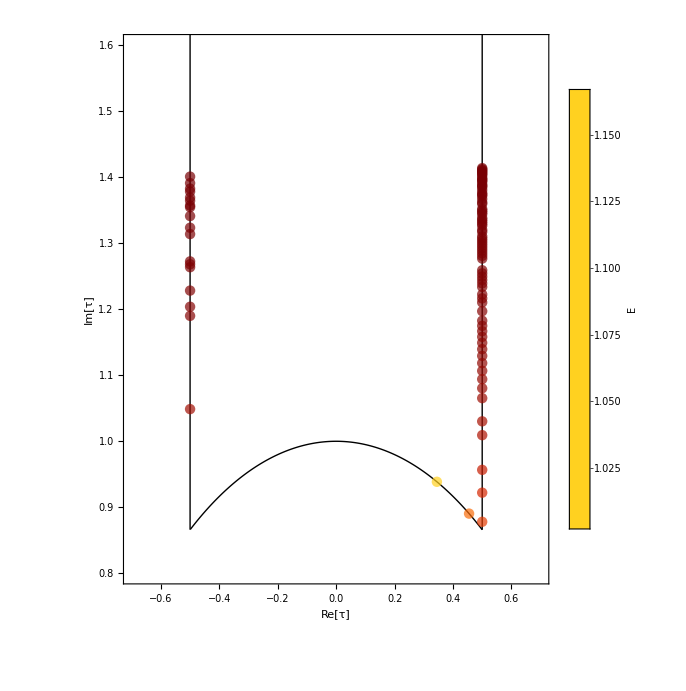

```mathematica
plotFundamentalDomainColored[tauFDCleaned,E2vals]
```

```mathematica
Length[tauFDCleaned]
Count[tauFDCleaned,_?(Im[#]>2.2&)]
Max[Im[tauFDCleaned]]
Min[Im[tauFDCleaned]]
```

89

0

1.41372

0.878062

```mathematica
Clear[plotFundamentalDomainColored, plotFundamentalDomainColoredOld, plotFundamentalDomain]
ClearAll[P4,quarticRoots,bestRootMatch,minRootDistance,mFromRoots,tauStdFromRoots,tauPhysicalFromRoots,nearestTauShift,buildRootGrid,buildTauGrid,tauDataIm,tauDataRe, unwrapTauByIntegerShift];
ClearAll[trackedSqrtValues,complexCutPeriod];
ClearAll[τ0List,τ2List]
```

```mathematica
ClearAll[tau0FDCleaned, tauConvention, tauDataIm, tauDataImRe]
ClearAll[P4,rootsRealOrdered,piAspin,piBspin,tauSpin];
ClearAll[qList, tauList, tau0ListClean, tau0, tauEs, tauFD, tauFromRoots,reduceTau, tauListNum]
```

## Turning pts

```mathematica
ClearAll[x0,r0,z,mu0,mu1,s,g,ν,ord,P,muEff,sinShift,cosShift,V0BW,V1BW,reduceRules,reduceExpr, Eseries, xRootSub, rRootSub, symmetricLimit];
```

```mathematica
(*---quartic w/ x = sin(q) *)
Clear[P4, quarticRoots, bestRootMatch, trackRoots1D,quarticRootsDebug,trackedSqrtValues]


P4[x_,Es_,mu0_,mu1_,mu2_]:=-x^4+mu2 x^3+(2-Es) x^2-(mu2+mu1) x+(Es-1-mu0);
(* --- numerical roots --- *)
quarticRoots[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:WKBprec]:=Module[{x,es,m0,m1,m2,roots},{es,m0,m1,m2}=SetPrecision[{Es,mu0,mu1,mu2},wp];
roots=NSolveValues[P4[x,es,m0,m1,m2]==0,x,WorkingPrecision->wp];
Chop[N[roots,wp],10^(-wp/2)]];

(*---match new roots to previous labeling by minimizing total motion---*)
bestRootMatch[prev_List,new_List]/;Length[prev]==Length[new]:=First@MinimalBy[Permutations[new],Total[Abs[#-prev]]&];

(*---numerical roots at high precision---*)
trackRoots1D[paramVals_List,mu0Fun_,mu1Fun_,EsFun_,wp_:WKBprec]:=Module[{rawRoots,tracked},rawRoots=Table[quarticRoots[EsFun[p],mu0Fun[p],mu1Fun[p],wp],{p,paramVals}];
tracked=ConstantArray[{},Length[paramVals]];
tracked[[1]]=SortBy[rawRoots[[1]],{Re[#],Im[#]}&];
Do[tracked[[k]]=bestRootMatch[tracked[[k-1]],rawRoots[[k]]],{k,2,Length[paramVals]}];
tracked];

quarticRootsDebug[Es_,mu0_,mu1_,wp_:80]:=Module[{x,es,m0,m1,poly,roots},{es,m0,m1}=SetPrecision[{Es,mu0,mu1},wp];
poly=P4[x,es,m0,m1];
Print["poly = ",poly];
roots=NSolveValues[poly==0,x,WorkingPrecision->wp];
Print["roots = ",roots];
roots];

trackedSqrtValues[vals_List]:=Module[{out,cand},out={Sqrt[vals[[1]]]};
Do[cand=Sqrt[vals[[k]]];
AppendTo[out,If[Abs[cand-out[[-1]]]<=Abs[-cand-out[[-1]]],cand,-cand]],{k,2,Length[vals]}];
out];

ClearAll[getRoots,getRootsTrackedList];

getRoots[paramAssoc_?AssociationQ,wp_:WKBprec]:=Module[{Es,mu0,mu1},Es=N@SetPrecision[paramAssoc["Es"],wp];
mu0=N@SetPrecision[paramAssoc["μ0"],wp];
mu1=N@SetPrecision[paramAssoc["μ1"],wp];
quarticRoots[Es,mu0,mu1,wp]];

getRootsTrackedList[assocList_List,wp_:WKBprec]:=Module[{raw,tracked},raw=getRoots[#,wp]&/@assocList;
tracked=ConstantArray[{},Length[raw]];
tracked[[1]]=SortBy[raw[[1]],{Re[#],Im[#]}&];
Do[tracked[[k]]=bestRootMatch[tracked[[k-1]],raw[[k]]],{k,2,Length[raw]}];
tracked];
```

```mathematica
ClearAll[poly,x,c,m,s];

poly[x_,c_,m_,s_]:=Expand[c^2*x*(x^2-1)^2+m*s*(1+x^2)+(1/4-m^2-s^2)*x];
```

Get analytical turning points

```mathematica
red=Reduce[P4[x,Es,m0,m1,m2]==0,x,Quartics->True];
analP4rootsList=Flatten[x/. {ToRules[red]}];
```

```mathematica
analP4rootsList[[1]]/.Es->Evals[[10]]/.μ0->mu0/.μ1->mu1/.replace$mu$Params/.μ2->Sqrt[2]ⅈ(-2)
```

0.-1.159676764759838238343979341606687716796906397 ⅈ

```mathematica
rootsTracked=getRootsTrackedList[assocListClean,48];
rootsTracked[[1;;10]]
```

NSolveValues::precw: The precision of the argument function ({0.07163889879054650966505590758970356546342372894+0.0088888888888888888811790067734364129137247800827 x$2077253+0.93697221232056460138437614659778773784637451172 x$2077253^2-x$2077253^4}) is less than WorkingPrecision (48).

NSolveValues::precw: The precision of the argument function ({0.05280078358452563232899867884384548233356326818+0.00500000000000000010408340855860842566471546888351 x$2077263+0.95204296641547436763630685163661837577819824219 x$2077263^2-x$2077263^4}) is less than WorkingPrecision (48).

NSolveValues::precw: The precision of the argument function ({0.0417940007619869240661214515597521312884055078+0.00320000000000000015334955527634974714601412415504 x$2077273+0.96130599923801307582493791414890438318252563477 x$2077273^2-x$2077273^4}) is less than WorkingPrecision (48).

General::stop: Further output of NSolveValues::precw will be suppressed during this calculation.

{{-0.998961856764264303773719195008357319526400433754,-0.03100011336361714056723878259720080694857129975-0.479057618855851181145178653798865836933138253557 ⅈ,-0.03100011336361714056723878259720080694857129975+0.479057618855851181145178653798865836933138253557 ⅈ,1.06096208349149858490819676020275893342354303325},{-0.999716182308897563458377388953846792545772741102,-0.008877361615506853891982546527255341386867099979-0.330454048398439120481924792157365676137341288318 ⅈ,-0.008877361615506853891982546527255341386867099979+0.330454048398439120481924792157365676137341288318 ⅈ,1.01747090553991127124234248200835747531950694106},{-0.999869849761120648246206409167435643296500829876,-0.004118855663817526487508431671414219121280080893-0.266561509307396822335639441967700764888474306592 ⅈ,-0.004118855663817526487508431671414219121280080893+0.266561509307396822335639441967700764888474306592 ⅈ,1.00810756108875570122122327251026408153906099166},{-0.999925614316024148854903103860252164710860562685,-0.002364869806960408466663883662580178006274624651-0.229247537318114144366032568226756126934299648259 ⅈ,-0.002364869806960408466663883662580178006274624651+0.229247537318114144366032568226756126934299648259 ⅈ,1.00465535392994496578823087118541252072340981199},{-0.999951931068524592414132049483805400990191512541,-0.001531632010778306286744777030971136357804224536-0.204127459380740527236570213406551067722564123587 ⅈ,-0.001531632010778306286744777030971136357804224536+0.204127459380740527236570213406551067722564123587 ⅈ,1.00301519509008120498762160354574767370579996161},{-0.999975200547240485134256388458885344069457079751,-0.000791799429081579002953651896878120364071418986-0.171586185200638866547497032883083310608499962275 ⅈ,-0.000791799429081579002953651896878120364071418986+0.171586185200638866547497032883083310608499962275 ⅈ,1.00155879940540364314016369225264158479759991772},{-0.999980946383320988235386727557417395461974607907,-0.000608657205115182077929770899039608921629203936-0.160221778996929831080250565339837419587209572993 ⅈ,-0.000608657205115182077929770899039608921629203936+0.160221778996929831080250565339837419587209572993 ⅈ,1.00119826079355135239124626935549661330523301578},{-0.999984904174075244858728557080968851124900878648,-0.000482399090295241330328035943907051628031593883-0.150848431236879248710703275211312453078945802209 ⅈ,-0.000482399090295241330328035943907051628031593883+0.150848431236879248710703275211312453078945802209 ⅈ,1.00094970235466572751938462896878295438096406641},{-0.99998774562057829924561078855459862669937936135,-0.000391698873517550915287205278186225130155630429-0.142946108187511400604365613135216877965191017876 ⅈ,-0.000391698873517550915287205278186225130155630429+0.142946108187511400604365613135216877965191017876 ⅈ,1.00077114336761340107618519911097107695969062221},{-0.999989854254479441409820677666436041576051693162,-0.000324360544518828897603087412638762371010757448-0.13616680365462018704230539923197884419301792552 ⅈ,-0.000324360544518828897603087412638762371010757448+0.13616680365462018704230539923197884419301792552 ⅈ,1.00063857534351709920502685249171356631807320806}}

## Expand about c=∞ for seeds to the root finders (fixed m)

```mathematica
red=Reduce[P4[x,Es,μ0,μ2]==0,x,Quartics->True];
analP4rootsList=Flatten[x/. {ToRules[red]}];
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

ReplaceAll::reps: {ToRules[Reduce[P4[x,Es,μ0,μ2]==0,x,Quartics→True]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
x/.{ToRules[ NRoots[poly[x,SetPrecision[10,WP],2,-2]==0,x]]}
```

{-1.00030306553069112159126150775727268640582933987203449657239-0.024868674331625572895990316093531430283968731394224169691528 ⅈ,-1.00030306553069112159126150775727268640582933987203449657239+0.024868674331625572895990316093531430283968731394224169691528 ⅈ,0.0436227458788336661907590541108391337626686746465071064935808714,0.77449472299669221193255045220139621186892843827200195219568826,1.18248866218585636505921350920231002718006156682555993445551}

```mathematica
Clear[roots]
roots[c_?NumericQ,m_Integer,s_Integer,wp_:rootPrec]:=SortBy[x/. {
ToRules@NRoots[poly[x,SetPrecision[c,wp],m,s]==0,x]} ,{Re,Im}];

rootsGrouped[c_?NumericQ,m_Integer,s_Integer,wp_:50]:=Module[{rr},
rr= roots[c,m,s,wp];
<|"near0"->SortBy[rr,Abs[#]&][[1]],"near+1"->SortBy[rr,Abs[#-1]&][[1;;2]],"near-1"->SortBy[rr,Abs[#+1]&][[1;;2]]|>];
```

```mathematica
rootsGrouped[10.,2,-2]
```

<|near0→0.04362274587883366619075905411083913376266867464651,near+1→{1.18248866218585636505921350920231002718006156683,0.774494722996692211932550452201396211868928438272},near-1→{-1.0003030655306911215912615077572726864058293399-0.0248686743316255728959903160935314302839687314 ⅈ,-1.0003030655306911215912615077572726864058293399+0.0248686743316255728959903160935314302839687314 ⅈ}|>

```mathematica
x0Seed[c_,m_,s_]:=-(m s)/c^2+m s (1/4-m^2-s^2)/c^4;

xPlusSeeds[c_,m_,s_]:=Module[{d=Sqrt[(m-s)^2-1/4]},{1+d/(2 c)-d (20 m^2-24 m s+20 s^2-5)/(256 c^3),1-d/(2 c)+d (20 m^2-24 m s+20 s^2-5)/(256 c^3)}];

xMinusSeeds[c_,m_,s_]:=Module[{d=Sqrt[(m+s)^2-1/4]},{-1+d/(2 c)-d (20 m^2+24 m s+20 s^2-5)/(256 c^3),-1-d/(2 c)+d (20 m^2+24 m s+20 s^2-5)/(256 c^3)}];
```

## GD reduction and recursion

```mathematica
MaTeX[" H(p,q)=\\frac{p^2}{2}+\\cos^2 q+\\frac{\\mu_0+\\mu_1 \\sin q}{\\cos^2 q} + \mu_2 \sin q",FontSize->12]
```

-Graphics-

```mathematica
MaTeX["(q,p) \\mapsto (\\arcsin(x),y \\partial_x \\arcsin(x))",FontSize->12]
```

```mathematica
-Graphics-
MaTeX["H=E \\implies f=0 \\text{\ Algebraic\  curve in weighted projective space } \\mathbb P^{(1,2,1)}",FontSize->12]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[μ0,μ1,μ2,Ε,x,y,z,f,J];
params = {μ0,μ1,μ2,Ε}


f=1/2 y^2+x^4-μ2 x^3 z+(Ε-2) x^2 z^2+(μ1+μ2) x z^3+(μ0-Ε+1) z^4;

J={D[f,x],D[f,y],D[f,z]};
```

{μ0,μ1,μ2,Ε}

```mathematica
(* The jacobian ideal contains y so we can elimnate it *)
```

```mathematica
(*represent a reduced polynomial as coords in the basis*)
coordsInBasis[poly_]:=Module[{rep=NFxz[poly],coeffs},(*express rep as linear combination of basisMonoms*)coeffs=LinearSolve[Transpose[CoefficientArrays[basisMonoms,{x,z}][[2]]],CoefficientArrays[{rep},{x,z}][[2]][[1]]];
coeffs];
```

```mathematica
Jxz={D[f,x],D[f,z]}/. y->0;
gbxz=GroebnerBasis[Jxz,{x,z},MonomialOrder->DegreeReverseLexicographic,CoefficientDomain->RationalFunctions,ParameterVariables->params];
```

```mathematica
gbxz
```

{x z^2 (-12 μ1-8 μ2-2 Ε μ2)+z^3 (-16+16 Ε-16 μ0-μ1 μ2-μ2^2)+x^2 z (16-8 Ε+3 μ2^2),z^3 (-4 μ1+2 Ε μ1+8 μ2-10 Ε μ2+12 μ0 μ2)+x^3 (-16+8 Ε-3 μ2^2)+x z^2 (16-16 Ε+4 Ε^2+9 μ1 μ2+9 μ2^2),z^4 (-64 μ1+64 Ε μ1-4 Ε^2 μ1-48 μ0 μ1-32 Ε μ2+28 Ε^2 μ2+16 μ0 μ2-32 Ε μ0 μ2-3 μ1^2 μ2-8 μ1 μ2^2+Ε μ1 μ2^2+4 μ2^3-8 Ε μ2^3+9 μ0 μ2^3)+x z^3 (16 Ε^2-8 Ε^3-64 μ0+32 Ε μ0-36 μ1^2-16 μ1 μ2-28 Ε μ1 μ2+16 μ2^2-24 Ε μ2^2+2 Ε^2 μ2^2-12 μ0 μ2^2+6 μ1 μ2^3+6 μ2^4),z^5}

```mathematica
gb=GroebnerBasis[J,{x,y,z},MonomialOrder->DegreeReverseLexicographic,CoefficientDomain->RationalFunctions,ParameterVariables->params]
```

{y,x z^2 (-12 μ1-8 μ2-2 Ε μ2)+z^3 (-16+16 Ε-16 μ0-μ1 μ2-μ2^2)+x^2 z (16-8 Ε+3 μ2^2),z^3 (-4 μ1+2 Ε μ1+8 μ2-10 Ε μ2+12 μ0 μ2)+x^3 (-16+8 Ε-3 μ2^2)+x z^2 (16-16 Ε+4 Ε^2+9 μ1 μ2+9 μ2^2),z^4 (-64 μ1+64 Ε μ1-4 Ε^2 μ1-48 μ0 μ1-32 Ε μ2+28 Ε^2 μ2+16 μ0 μ2-32 Ε μ0 μ2-3 μ1^2 μ2-8 μ1 μ2^2+Ε μ1 μ2^2+4 μ2^3-8 Ε μ2^3+9 μ0 μ2^3)+x z^3 (16 Ε^2-8 Ε^3-64 μ0+32 Ε μ0-36 μ1^2-16 μ1 μ2-28 Ε μ1 μ2+16 μ2^2-24 Ε μ2^2+2 Ε^2 μ2^2-12 μ0 μ2^2+6 μ1 μ2^3+6 μ2^4),z^5}

```mathematica
leadMons=DeleteDuplicates[First@MonomialList[#,{x,y,z},DegreeReverseLexicographic]&/@gb];

leadExps=Exponent[#,{x,y,z},List]&/@leadMons
```

{{{0},{1},{0}},{{2},{0},{1}},{{3},{0},{0}},{{1},{0},{3}},{{0},{0},{5}}}

```mathematica
Clear[nb]
```

```mathematica
ClearAll[MonomialDividesQ,StandardMonomialsFromGB];

(*MonomialDividesQ[a,b,vars] returns True if the monomial a divides the monomial b,with respect to the variables in vars.Example:a=x^2 z,b=x^3 z^4->True because the exponent vector of a is componentwise<=that of b.*)
MonomialDividesQ[a_,b_,vars_List]:=Module[{ea,eb},(*exponent vectors of a and b with respect to vars*)ea=Exponent[a,vars];
eb=Exponent[b,vars];
(*a divides b iff every exponent in b is at least the one in a*)And@@Thread[eb>=ea]]

(*StandardMonomialsFromGB[gb,vars,order] computes the standard monomials (the "normal basis") for the quotient ring R/<gb>,assuming the quotient is finite-dimensional.The idea is:1. extract the leading monomial of each Groebner basis element;
2. find bounds coming from pure powers x_i^m in the leading ideal;
3. generate all monomials below those bounds;
4. discard those divisible by any leading monomial.The remaining monomials form a basis of the quotient as a vector space over the coefficient field.*)
StandardMonomialsFromGB[gb_List,vars_List,order_:DegreeReverseLexicographic]:=Module[{leadMons,exps,pureBounds,cands},(*Extract the leading monomial of each Groebner basis element.MonomialList[...,vars,order] returns the monomials ordered according to the chosen monomial order,so First[...] is the leading monomial.*)leadMons=DeleteDuplicates[First@MonomialList[#,vars,order]&/@gb];
(*exponent vectors of those leading monomials*)exps=Exponent[#,vars]&/@leadMons;
(*For each variable vars[[i]],look for pure powers vars[[i]]^m among the leading monomials.If such a pure power exists,then exponents in that variable only need to range from 0 up to m-1. Example:if x^3 is in the leading ideal,then standard monomials can only contain x^0,x^1,or x^2. If no pure power is found for some variable,this simple box search fails,and we return $Failed.*)pureBounds=Table[With[{hits=Cases[exps,e_/;Count[e,_?(#>0&)]==1&&e[[i]]>0:>e[[i]]]},If[hits==={},Return[$Failed],Min[hits]]],{i,Length[vars]}];
(*Generate all candidate monomials inside the exponent box 0<=e_i<=pureBounds[[i]]-1.*)cands=Times@@(vars^#)&/@Tuples[Range[0,#-1]&/@pureBounds];
(*Keep only those candidate monomials that are NOT divisible by any leading monomial.These are the standard monomials.*)Select[cands,Function[m,NoneTrue[leadMons,MonomialDividesQ[#,m,vars]&]]]]
```

```mathematica
nb=StandardMonomialsFromGB[gb,{x,y,z},DegreeReverseLexicographic]
```

{1,z,z^2,z^3,z^4,x,x z,x z^2,x^2}

```mathematica
NFxz[poly_]:=PolynomialReduce[poly,gbxz,{x,z}][[2]]//Expand;

(*generate candidate monomials up to some degree bound*)
cands=Flatten@Table[x^a z^b,{a,0,6},{b,0,6}];

nfs=NFxz/@cands;

(*pick a linearly independent subset by treating coefficients as symbols*)
basisMonoms=DeleteDuplicates[nfs];
basisMonoms=Select[basisMonoms,#=!=0&];
basisMonoms;
Length[basisMonoms]
```

15

```mathematica
ClearAll[μ0,μ1,μ2,Ε,x,y,ζ,fUn,JUn];

fUn=1/2 y^2 ζ^2+x^4-μ2 x^3 ζ+(Ε-2) x^2 ζ^2+(μ1+μ2) x ζ^3+(μ0-Ε+1) ζ^4;

JUn=D[fUn,#]&/@{x,y,ζ};
```

```mathematica
Expand/@JUn
```

{4 x^3-4 x ζ^2+2 x Ε ζ^2+ζ^3 μ1-3 x^2 ζ μ2+ζ^3 μ2,y ζ^2,-4 x^2 ζ+y^2 ζ+2 x^2 Ε ζ+4 ζ^3-4 Ε ζ^3+4 ζ^3 μ0+3 x ζ^2 μ1-x^3 μ2+3 x ζ^2 μ2}

```mathematica
gbUn=GroebnerBasis[JUn,{x,y,ζ},MonomialOrder->DegreeReverseLexicographic,CoefficientDomain->RationalFunctions,ParameterVariables->params];
```

```mathematica
gbUn
```

{y ζ^2,-4 y^2 ζ+x ζ^2 (-12 μ1-8 μ2-2 Ε μ2)+ζ^3 (-16+16 Ε-16 μ0-μ1 μ2-μ2^2)+x^2 ζ (16-8 Ε+3 μ2^2),3 y^2 ζ μ2+ζ^3 (-4 μ1+2 Ε μ1+8 μ2-10 Ε μ2+12 μ0 μ2)+x^3 (-16+8 Ε-3 μ2^2)+x ζ^2 (16-16 Ε+4 Ε^2+9 μ1 μ2+9 μ2^2),x y^2 ζ (-16+8 Ε-3 μ2^2)+ζ^4 (-64 μ1+64 Ε μ1-4 Ε^2 μ1-48 μ0 μ1-32 Ε μ2+28 Ε^2 μ2+16 μ0 μ2-32 Ε μ0 μ2-3 μ1^2 μ2-8 μ1 μ2^2+Ε μ1 μ2^2+4 μ2^3-8 Ε μ2^3+9 μ0 μ2^3)+x ζ^3 (16 Ε^2-8 Ε^3-64 μ0+32 Ε μ0-36 μ1^2-16 μ1 μ2-28 Ε μ1 μ2+16 μ2^2-24 Ε μ2^2+2 Ε^2 μ2^2-12 μ0 μ2^2+6 μ1 μ2^3+6 μ2^4),ζ^5 (64 μ1-64 Ε μ1+4 Ε^2 μ1+48 μ0 μ1+32 Ε μ2-28 Ε^2 μ2-16 μ0 μ2+32 Ε μ0 μ2+3 μ1^2 μ2+8 μ1 μ2^2-Ε μ1 μ2^2-4 μ2^3+8 Ε μ2^3-9 μ0 μ2^3)+x ζ^4 (-16 Ε^2+8 Ε^3+64 μ0-32 Ε μ0+36 μ1^2+16 μ1 μ2+28 Ε μ1 μ2-16 μ2^2+24 Ε μ2^2-2 Ε^2 μ2^2+12 μ0 μ2^2-6 μ1 μ2^3-6 μ2^4),y^4 ζ (-64 Ε^2+32 Ε^3+256 μ0-128 Ε μ0+144 μ1^2+64 μ1 μ2+112 Ε μ1 μ2-64 μ2^2+96 Ε μ2^2-8 Ε^2 μ2^2+48 μ0 μ2^2-24 μ1 μ2^3-24 μ2^4)+ζ^5 (256 Ε^4-384 Ε^5+128 Ε^6-2048 Ε^2 μ0+3072 Ε^3 μ0-768 Ε^4 μ0-128 Ε^5 μ0+4096 μ0^2-6144 Ε μ0^2+1024 Ε^3 μ0^2+4096 μ0^3-2048 Ε μ0^3-4096 μ1^2+8192 Ε μ1^2-4992 Ε^2 μ1^2+896 Ε^3 μ1^2+32 Ε^4 μ1^2-4608 μ0 μ1^2+4608 Ε μ0 μ1^2-1152 Ε^2 μ0 μ1^2-432 μ1^4+216 Ε μ1^4-4096 Ε μ1 μ2+7680 Ε^2 μ1 μ2-4224 Ε^3 μ1 μ2+704 Ε^4 μ1 μ2+2048 μ0 μ1 μ2-7680 Ε μ0 μ1 μ2+4608 Ε^2 μ0 μ1 μ2-640 Ε^3 μ0 μ1 μ2+3072 μ0^2 μ1 μ2-1536 Ε μ0^2 μ1 μ2-1152 μ1^3 μ2+288 Ε μ1^3 μ2+144 Ε^2 μ1^3 μ2-512 Ε^2 μ2^2+768 Ε^3 μ2^2-144 Ε^4 μ2^2-80 Ε^5 μ2^2-2048 μ0 μ2^2+5120 Ε μ0 μ2^2-5376 Ε^2 μ0 μ2^2+1792 Ε^3 μ0 μ2^2+80 Ε^4 μ0 μ2^2-768 μ0^2 μ2^2+2304 Ε μ0^2 μ2^2-1536 Ε^2 μ0^2 μ2^2+768 μ0^3 μ2^2-1664 μ1^2 μ2^2+768 Ε μ1^2 μ2^2+72 Ε^2 μ1^2 μ2^2-20 Ε^3 μ1^2 μ2^2-960 μ0 μ1^2 μ2^2+480 Ε μ0 μ1^2 μ2^2-81 μ1^4 μ2^2+512 μ1 μ2^3-2688 Ε μ1 μ2^3+2208 Ε^2 μ1 μ2^3-424 Ε^3 μ1 μ2^3+768 μ0 μ1 μ2^3-1728 Ε μ0 μ1 μ2^3+384 Ε^2 μ0 μ1 μ2^3+576 μ0^2 μ1 μ2^3-152 μ1^3 μ2^3-86 Ε μ1^3 μ2^3+256 μ2^4-384 Ε μ2^4-96 Ε^2 μ2^4+160 Ε^3 μ2^4+12 Ε^4 μ2^4-768 μ0 μ2^4+1536 Ε μ0 μ2^4-840 Ε^2 μ0 μ2^4-12 Ε^3 μ0 μ2^4-720 μ0^2 μ2^4+648 Ε μ0^2 μ2^4+24 μ1^2 μ2^4-252 Ε μ1^2 μ2^4+3 Ε^2 μ1^2 μ2^4-18 μ0 μ1^2 μ2^4+288 μ1 μ2^5-408 Ε μ1 μ2^5+60 Ε^2 μ1 μ2^5+72 μ0 μ1 μ2^5-54 Ε μ0 μ1 μ2^5+12 μ1^3 μ2^5+112 μ2^6-80 Ε μ2^6-24 Ε^2 μ2^6-72 μ0 μ2^6+108 Ε μ0 μ2^6-81 μ0^2 μ2^6+36 μ1^2 μ2^6+36 μ1 μ2^7+12 μ2^8),ζ^6}

```mathematica
ClearAll[NormalFormGD];

Options[NormalFormGD] = {
   MonomialOrder -> DegreeReverseLexicographic,
   CoefficientDomain -> RationalFunctions,
   ParameterVariables -> {}
};

NormalFormGD[poly_, gens_List, vars_List, OptionsPattern[]] :=
 Module[{qs, r},
  {qs, r} = PolynomialReduce[
    poly, gens, vars,
    MonomialOrder -> OptionValue[MonomialOrder],
    CoefficientDomain -> OptionValue[CoefficientDomain],
    ParameterVariables -> OptionValue[ParameterVariables]
  ];
  <|"Remainder" -> r, "Quotients" -> qs|>
]
```

```mathematica
ClearAll[WeightedDegreeMonomial,WeightedDegree,WeightedHomogeneousComponents];

WeightedDegreeMonomial[mon_,vars_List,weights_List]:=weights.Exponent[mon,vars];

WeightedHomogeneousComponents[poly_,vars_List,weights_List]:=Module[{mons,grouped},mons=MonomialList[Expand[poly],vars];
grouped=GroupBy[mons,WeightedDegreeMonomial[#,vars,weights]&,Total];
KeySort[grouped]]

WeightedDegree[poly_,vars_List,weights_List]:=Module[{hcs=WeightedHomogeneousComponents[poly,vars,weights]},If[hcs===<||>,-Infinity,Max[Keys[hcs]]]]
```

```mathematica
ClearAll[PoleReduceGD];

Options[PoleReduceGD]=Options[NormalFormGD];

PoleReduceGD[poly_,gens_List,vars_List,weights_List,OptionsPattern[]]:=Module[{nf,q,hcs,wdim,degf,out=0},nf=NormalFormGD[poly,gens,vars,MonomialOrder->OptionValue[MonomialOrder],CoefficientDomain->OptionValue[CoefficientDomain],ParameterVariables->OptionValue[ParameterVariables]];
q=Total@MapThread[D[#1,#2]&,{nf["Quotients"],vars}];
hcs=WeightedHomogeneousComponents[q,vars,weights];
wdim=Total[weights];
degf=WeightedDegree[gens[[1]],vars,weights]+weights[[1]];
out=Total@KeyValueMap[#2/((#1+wdim)/degf)&,hcs];
Expand[out+nf["Remainder"]]]
```

```mathematica
ClearAll[PoleReduceFullGD];

Options[PoleReduceFullGD]=Options[NormalFormGD];

PoleReduceFullGD[poly_,gens_List,vars_List,weights_List,OptionsPattern[]]:=Module[{wdim,degf,maxPoleOrder,out,n},wdim=Total[weights];
degf=WeightedDegree[gens[[1]],vars,weights]+weights[[1]];
maxPoleOrder=(WeightedDegree[poly,vars,weights]+wdim)/degf;
n=Ceiling[maxPoleOrder];
out=poly;
Do[out=PoleReduceGD[out,gens,vars,weights,MonomialOrder->OptionValue[MonomialOrder],CoefficientDomain->OptionValue[CoefficientDomain],ParameterVariables->OptionValue[ParameterVariables]],{n}];
Expand[out]]
```

```mathematica
redOpts=Sequence[MonomialOrder->DegreeReverseLexicographic,CoefficientDomain->RationalFunctions,ParameterVariables->params];

nfTest=NormalFormGD[x^5 ζ^2,JUn,{x,y,ζ},redOpts]

prTest=PoleReduceGD[x^5 ζ^2,JUn,{x,y,ζ},{1,1,1},redOpts]

prFullTest=PoleReduceFullGD[x^5 ζ^2,JUn,{x,y,ζ},{1,2,1},redOpts]
```

<|Remainder→1/32 x ζ^6 (32-32 Ε+8 Ε^2-6 μ1 μ2+12 μ2^2-9 Ε μ2^2)+1/64 ζ^7 (-16 μ1+8 Ε μ1-16 μ2+8 Ε μ2-9 μ1 μ2^2-9 μ2^3)+1/64 x^2 ζ^5 (-16 μ1+80 μ2-48 Ε μ2+27 μ2^3),Quotients→{(x^2 ζ^2)/4+3/16 x ζ^3 μ2+1/64 ζ^4 (16-8 Ε+9 μ2^2),0,0}|>

(x ζ^2)/3+x ζ^6-x Ε ζ^6+1/4 x Ε^2 ζ^6-1/4 x^2 ζ^5 μ1-(ζ^7 μ1)/4+1/8 Ε ζ^7 μ1+(ζ^3 μ2)/8+5/4 x^2 ζ^5 μ2-3/4 x^2 Ε ζ^5 μ2-(ζ^7 μ2)/4+1/8 Ε ζ^7 μ2-3/16 x ζ^6 μ1 μ2+3/8 x ζ^6 μ2^2-9/32 x Ε ζ^6 μ2^2-9/64 ζ^7 μ1 μ2^2+27/64 x^2 ζ^5 μ2^3-(9 ζ^7 μ2^3)/64

(2 x ζ^2)/7+x ζ^6-x Ε ζ^6+1/4 x Ε^2 ζ^6-1/4 x^2 ζ^5 μ1-(ζ^7 μ1)/4+1/8 Ε ζ^7 μ1+(3 ζ^3 μ2)/28+5/4 x^2 ζ^5 μ2-3/4 x^2 Ε ζ^5 μ2-(ζ^7 μ2)/4+1/8 Ε ζ^7 μ2-3/16 x ζ^6 μ1 μ2+3/8 x ζ^6 μ2^2-9/32 x Ε ζ^6 μ2^2-9/64 ζ^7 μ1 μ2^2+27/64 x^2 ζ^5 μ2^3-(9 ζ^7 μ2^3)/64

```mathematica
varsUn={x,y,ζ};
weightsUn={2,2,2};
params={μ0,μ1,μ2,Ε};
```

```mathematica
res=PoleReduceFullGD[gbUn[[2]],JUn,varsUn,weightsUn,MonomialOrder->DegreeReverseLexicographic,CoefficientDomain->RationalFunctions,ParameterVariables->params];

Factor@Together@Simplify[res]
```

ζ (16 x^2-4 y^2-8 x^2 Ε-16 ζ^2+16 Ε ζ^2-16 ζ^2 μ0-12 x ζ μ1-8 x ζ μ2-2 x Ε ζ μ2-ζ^2 μ1 μ2+3 x^2 μ2^2-ζ^2 μ2^2)

```mathematica
ClearAll[WeightedHomogeneousComponents,WeightedDegree,WeightedMonomialsOfDegree,LiftHomogeneousComponent,LiftToGenerators,MakeGDIdeal,NormalFormGD,PoleReduceGD,PoleReduceFullGD];

WeightedHomogeneousComponents[poly_,vars_List,weights_List]:=Module[{rules},rules=CoefficientRules[Expand[poly],vars];
KeySort@GroupBy[rules,weights.First[#]&,Total[(#[[2]]*Times@@(vars^#[[1]]))&/@#]&]];

WeightedDegree[poly_,vars_List,weights_List]:=Module[{hcs=WeightedHomogeneousComponents[poly,vars,weights]},If[hcs===<||>,-Infinity,Max[Keys[hcs]]]];

WeightedMonomialsOfDegree[vars_List,weights_List,d_Integer]:=Module[{bounds,exps},If[d<0,Return[{}]];
bounds=Floor[d/weights];
exps=Select[Tuples[Range[0,#]&/@bounds],weights.#==d&];
Times@@(vars^#)&/@exps];

LiftHomogeneousComponent[target_,gens_List,vars_List,weights_List]:=Module[{dTarget,degs,bases,coeffs,qs,unknowns,expr,eqns,sol,c},If[Expand[target]===0,Return[ConstantArray[0,Length[gens]]]];
dTarget=WeightedDegree[target,vars,weights];
degs=WeightedDegree[#,vars,weights]&/@gens;
c=Unique["c"];
bases=WeightedMonomialsOfDegree[vars,weights,dTarget-#]&/@degs;
coeffs=Table[Array[c[i,#]&,Length[bases[[i]]]],{i,Length[gens]}];
qs=Table[If[bases[[i]]==={},0,Total[coeffs[[i]]*bases[[i]]]],{i,Length[gens]}];
expr=Expand[Total[qs*gens]-target];
eqns=Thread[(Last/@CoefficientRules[expr,vars])==0];
unknowns=Flatten[coeffs];
sol=Solve[eqns,unknowns];
If[sol==={},$Failed,Expand/@(qs/. First[sol])]];

LiftToGenerators[target_,gens_List,vars_List,weights_List]:=Module[{hcs,total,comp},hcs=WeightedHomogeneousComponents[target,vars,weights];
total=ConstantArray[0,Length[gens]];
KeyValueMap[(comp=LiftHomogeneousComponent[#2,gens,vars,weights];
If[comp===$Failed,Return[$Failed]];
total+=comp;)&,hcs];
Expand/@total];

MakeGDIdeal[gens_List,vars_List,weights_List,order_:DegreeReverseLexicographic,gbOpts___]:=<|"Generators"->gens,"Variables"->vars,"Weights"->weights,"Order"->order,"GroebnerBasis"->GroebnerBasis[gens,vars,MonomialOrder->order,gbOpts]|>;

NormalFormGD[poly_,J_Association]:=Module[{r,l},r=Last@PolynomialReduce[poly,J["GroebnerBasis"],J["Variables"],MonomialOrder->J["Order"]];
l=LiftToGenerators[Expand[poly-r],J["Generators"],J["Variables"],J["Weights"]];
<|"Remainder"->Expand[r],"Quotients"->l|>];

PoleReduceGD[poly_,J_Association]:=Module[{qr,xs,q,hcs,wdim,degf,out=0},qr=NormalFormGD[poly,J];
xs=J["Variables"];
q=Expand@Total@MapThread[D[#1,#2]&,{qr["Quotients"],xs}];
hcs=WeightedHomogeneousComponents[q,xs,J["Weights"]];
wdim=Total[J["Weights"]];
degf=WeightedDegree[J["Generators"][[1]],xs,J["Weights"]]+J["Weights"][[1]];
KeyValueMap[(out+=#2/((#1+wdim)/degf))&,hcs];
Expand[out+qr["Remainder"]]];

PoleReduceFullGD[poly_,J_Association]:=Module[{xs,wdim,degf,maxPoleOrder,out},xs=J["Variables"];
wdim=Total[J["Weights"]];
degf=WeightedDegree[J["Generators"][[1]],xs,J["Weights"]]+J["Weights"][[1]];
maxPoleOrder=Ceiling[(WeightedDegree[poly,xs,J["Weights"]]+wdim)/degf];
out=PoleReduceGD[poly,J];
Do[out=PoleReduceGD[out,J],{maxPoleOrder}];
Together@FullSimplify[out]];
```

```mathematica
JData=MakeGDIdeal[JUn,{x,y,ζ},{1,1,1},DegreeReverseLexicographic,CoefficientDomain->RationalFunctions,ParameterVariables->params];
```

```mathematica
JData
```

<|Generators→{4 x^3+2 x (-2+Ε) ζ^2-3 x^2 ζ μ2+ζ^3 (μ1+μ2),y ζ^2,y^2 ζ+2 x^2 (-2+Ε) ζ+4 ζ^3 (1-Ε+μ0)-x^3 μ2+3 x ζ^2 (μ1+μ2)},Variables→{x,y,ζ},Weights→{1,1,1},Order→DegreeReverseLexicographic,GroebnerBasis→{y ζ^2,-4 y^2 ζ+x ζ^2 (-12 μ1-8 μ2-2 Ε μ2)+ζ^3 (-16+16 Ε-16 μ0-μ1 μ2-μ2^2)+x^2 ζ (16-8 Ε+3 μ2^2),3 y^2 ζ μ2+ζ^3 (-4 μ1+2 Ε μ1+8 μ2-10 Ε μ2+12 μ0 μ2)+x^3 (-16+8 Ε-3 μ2^2)+x ζ^2 (16-16 Ε+4 Ε^2+9 μ1 μ2+9 μ2^2),x y^2 ζ (-16+8 Ε-3 μ2^2)+ζ^4 (-64 μ1+64 Ε μ1-4 Ε^2 μ1-48 μ0 μ1-32 Ε μ2+28 Ε^2 μ2+16 μ0 μ2-32 Ε μ0 μ2-3 μ1^2 μ2-8 μ1 μ2^2+Ε μ1 μ2^2+4 μ2^3-8 Ε μ2^3+9 μ0 μ2^3)+x ζ^3 (16 Ε^2-8 Ε^3-64 μ0+32 Ε μ0-36 μ1^2-16 μ1 μ2-28 Ε μ1 μ2+16 μ2^2-24 Ε μ2^2+2 Ε^2 μ2^2-12 μ0 μ2^2+6 μ1 μ2^3+6 μ2^4),ζ^5 (64 μ1-64 Ε μ1+4 Ε^2 μ1+48 μ0 μ1+32 Ε μ2-28 Ε^2 μ2-16 μ0 μ2+32 Ε μ0 μ2+3 μ1^2 μ2+8 μ1 μ2^2-Ε μ1 μ2^2-4 μ2^3+8 Ε μ2^3-9 μ0 μ2^3)+x ζ^4 (-16 Ε^2+8 Ε^3+64 μ0-32 Ε μ0+36 μ1^2+16 μ1 μ2+28 Ε μ1 μ2-16 μ2^2+24 Ε μ2^2-2 Ε^2 μ2^2+12 μ0 μ2^2-6 μ1 μ2^3-6 μ2^4),y^4 ζ (-64 Ε^2+32 Ε^3+256 μ0-128 Ε μ0+144 μ1^2+64 μ1 μ2+112 Ε μ1 μ2-64 μ2^2+96 Ε μ2^2-8 Ε^2 μ2^2+48 μ0 μ2^2-24 μ1 μ2^3-24 μ2^4)+ζ^5 (256 Ε^4-384 Ε^5+128 Ε^6-2048 Ε^2 μ0+3072 Ε^3 μ0-768 Ε^4 μ0-128 Ε^5 μ0+4096 μ0^2-6144 Ε μ0^2+1024 Ε^3 μ0^2+4096 μ0^3-2048 Ε μ0^3-4096 μ1^2+8192 Ε μ1^2-4992 Ε^2 μ1^2+896 Ε^3 μ1^2+32 Ε^4 μ1^2-4608 μ0 μ1^2+4608 Ε μ0 μ1^2-1152 Ε^2 μ0 μ1^2-432 μ1^4+216 Ε μ1^4-4096 Ε μ1 μ2+7680 Ε^2 μ1 μ2-4224 Ε^3 μ1 μ2+704 Ε^4 μ1 μ2+2048 μ0 μ1 μ2-7680 Ε μ0 μ1 μ2+4608 Ε^2 μ0 μ1 μ2-640 Ε^3 μ0 μ1 μ2+3072 μ0^2 μ1 μ2-1536 Ε μ0^2 μ1 μ2-1152 μ1^3 μ2+288 Ε μ1^3 μ2+144 Ε^2 μ1^3 μ2-512 Ε^2 μ2^2+768 Ε^3 μ2^2-144 Ε^4 μ2^2-80 Ε^5 μ2^2-2048 μ0 μ2^2+5120 Ε μ0 μ2^2-5376 Ε^2 μ0 μ2^2+1792 Ε^3 μ0 μ2^2+80 Ε^4 μ0 μ2^2-768 μ0^2 μ2^2+2304 Ε μ0^2 μ2^2-1536 Ε^2 μ0^2 μ2^2+768 μ0^3 μ2^2-1664 μ1^2 μ2^2+768 Ε μ1^2 μ2^2+72 Ε^2 μ1^2 μ2^2-20 Ε^3 μ1^2 μ2^2-960 μ0 μ1^2 μ2^2+480 Ε μ0 μ1^2 μ2^2-81 μ1^4 μ2^2+512 μ1 μ2^3-2688 Ε μ1 μ2^3+2208 Ε^2 μ1 μ2^3-424 Ε^3 μ1 μ2^3+768 μ0 μ1 μ2^3-1728 Ε μ0 μ1 μ2^3+384 Ε^2 μ0 μ1 μ2^3+576 μ0^2 μ1 μ2^3-152 μ1^3 μ2^3-86 Ε μ1^3 μ2^3+256 μ2^4-384 Ε μ2^4-96 Ε^2 μ2^4+160 Ε^3 μ2^4+12 Ε^4 μ2^4-768 μ0 μ2^4+1536 Ε μ0 μ2^4-840 Ε^2 μ0 μ2^4-12 Ε^3 μ0 μ2^4-720 μ0^2 μ2^4+648 Ε μ0^2 μ2^4+24 μ1^2 μ2^4-252 Ε μ1^2 μ2^4+3 Ε^2 μ1^2 μ2^4-18 μ0 μ1^2 μ2^4+288 μ1 μ2^5-408 Ε μ1 μ2^5+60 Ε^2 μ1 μ2^5+72 μ0 μ1 μ2^5-54 Ε μ0 μ1 μ2^5+12 μ1^3 μ2^5+112 μ2^6-80 Ε μ2^6-24 Ε^2 μ2^6-72 μ0 μ2^6+108 Ε μ0 μ2^6-81 μ0^2 μ2^6+36 μ1^2 μ2^6+36 μ1 μ2^7+12 μ2^8),ζ^6}|>

```mathematica
ClearAll[mhat,delta1,delta2,g1,g2,a,PList];

mhat[U_]:=Expand[(2 y D[U,y]+x D[U,x]+z D[U,z]+4 U)/4];

delta1[U_]:=Expand[z (D[U,x]-D[f,x] mhat[U])];

delta2[U_]:=Expand[D[U,y]-D[f,y] mhat[U]];

g1[U_]:=Expand[I y ((z^2-x^2) delta1[U]-z x y delta2[U])];

g2[U_]:=Expand[(1/2 z^4-z^2 x^2+1/2 x^4) delta1[delta1[U]]+y z (-z^2 x+x^3) delta2[delta1[U]]+1/2 y^2 x^2 delta2[z^2 delta2[U]]+1/2 z (-z^2+x^2) (y z delta2[U]+x delta1[U])];
```

```mathematica
a[-1]=0;
a[0]=1;

a[n_Integer?Positive]:=a[n]=Expand[g1[a[n-1]]+g2[a[n-2]]];
```

```mathematica
Table[a[n],{n,0,5}]
```

```mathematica
PList[max_Integer?NonNegative]:=Table[a[n],{n,0,max}]
```

```mathematica
ClearAll[PListIter];

PListIter[max_Integer?NonNegative]:=Module[{n=0,an=1,bn=0,ao=0,out={}},While[n<=max,AppendTo[out,an];
n++;
bn=ao;
ao=an;
an=Expand[g1[an]+g2[bn]];];
out]
```

```mathematica
P=Table[a[n],{n,0,2}];
```

```mathematica
P
```

{1,4 ⅈ x^5 y z+ⅈ x y^3 z-8 ⅈ x^3 y z^3+4 ⅈ x y z^5+2 ⅈ x^3 y z^3 Ε-2 ⅈ x y z^5 Ε+ⅈ x^2 y z^4 μ1-ⅈ y z^6 μ1-3 ⅈ x^4 y z^2 μ2+4 ⅈ x^2 y z^4 μ2-ⅈ y z^6 μ2,-8 x^6 z^2+16 x^10 z^2-x^2 y^2 z^2+32 x^6 y^2 z^2-48 x^10 y^2 z^2+5 x^2 y^4 z^2-24 x^6 y^4 z^2-3 x^2 y^6 z^2+18 x^4 z^4-64 x^8 z^4+(y^2 z^4)/2-68 x^4 y^2 z^4+192 x^8 y^2 z^4-y^4 z^4+48 x^4 y^4 z^4-12 x^2 z^6+96 x^6 z^6+40 x^2 y^2 z^6-288 x^6 y^2 z^6-24 x^2 y^4 z^6+2 z^8-64 x^4 z^8-4 y^2 z^8+192 x^4 y^2 z^8+16 x^2 z^10-48 x^2 y^2 z^10-2 x^4 z^4 Ε+16 x^8 z^4 Ε+12 x^4 y^2 z^4 Ε-48 x^8 y^2 z^4 Ε-12 x^4 y^4 z^4 Ε+3 x^2 z^6 Ε-48 x^6 z^6 Ε-14 x^2 y^2 z^6 Ε+144 x^6 y^2 z^6 Ε+12 x^2 y^4 z^6 Ε-z^8 Ε+48 x^4 z^8 Ε+2 y^2 z^8 Ε-144 x^4 y^2 z^8 Ε-16 x^2 z^10 Ε+48 x^2 y^2 z^10 Ε+4 x^6 z^6 Ε^2-12 x^6 y^2 z^6 Ε^2-8 x^4 z^8 Ε^2+24 x^4 y^2 z^8 Ε^2+4 x^2 z^10 Ε^2-12 x^2 y^2 z^10 Ε^2-1/2 x^3 z^5 μ1+8 x^7 z^5 μ1+5 x^3 y^2 z^5 μ1-24 x^7 y^2 z^5 μ1-6 x^3 y^4 z^5 μ1+1/2 x z^7 μ1-24 x^5 z^7 μ1-5 x y^2 z^7 μ1+72 x^5 y^2 z^7 μ1+6 x y^4 z^7 μ1+24 x^3 z^9 μ1-72 x^3 y^2 z^9 μ1-8 x z^11 μ1+24 x y^2 z^11 μ1+4 x^5 z^7 Ε μ1-12 x^5 y^2 z^7 Ε μ1-8 x^3 z^9 Ε μ1+24 x^3 y^2 z^9 Ε μ1+4 x z^11 Ε μ1-12 x y^2 z^11 Ε μ1+x^4 z^8 μ1^2-3 x^4 y^2 z^8 μ1^2-2 x^2 z^10 μ1^2+6 x^2 y^2 z^10 μ1^2+z^12 μ1^2-3 y^2 z^12 μ1^2+9/2 x^5 z^3 μ2-24 x^9 z^3 μ2-21 x^5 y^2 z^3 μ2+72 x^9 y^2 z^3 μ2+18 x^5 y^4 z^3 μ2-8 x^3 z^5 μ2+80 x^7 z^5 μ2+32 x^3 y^2 z^5 μ2-240 x^7 y^2 z^5 μ2-24 x^3 y^4 z^5 μ2+7/2 x z^7 μ2-96 x^5 z^7 μ2-11 x y^2 z^7 μ2+288 x^5 y^2 z^7 μ2+6 x y^4 z^7 μ2+48 x^3 z^9 μ2-144 x^3 y^2 z^9 μ2-8 x z^11 μ2+24 x y^2 z^11 μ2-12 x^7 z^5 Ε μ2+36 x^7 y^2 z^5 Ε μ2+28 x^5 z^7 Ε μ2-84 x^5 y^2 z^7 Ε μ2-20 x^3 z^9 Ε μ2+60 x^3 y^2 z^9 Ε μ2+4 x z^11 Ε μ2-12 x y^2 z^11 Ε μ2-6 x^6 z^6 μ1 μ2+18 x^6 y^2 z^6 μ1 μ2+14 x^4 z^8 μ1 μ2-42 x^4 y^2 z^8 μ1 μ2-10 x^2 z^10 μ1 μ2+30 x^2 y^2 z^10 μ1 μ2+2 z^12 μ1 μ2-6 y^2 z^12 μ1 μ2+9 x^8 z^4 μ2^2-27 x^8 y^2 z^4 μ2^2-24 x^6 z^6 μ2^2+72 x^6 y^2 z^6 μ2^2+22 x^4 z^8 μ2^2-66 x^4 y^2 z^8 μ2^2-8 x^2 z^10 μ2^2+24 x^2 y^2 z^10 μ2^2+z^12 μ2^2-3 y^2 z^12 μ2^2}

```mathematica
P[[2]]
```

4 ⅈ x^5 y z+ⅈ x y^3 z-8 ⅈ x^3 y z^3+4 ⅈ x y z^5+2 ⅈ x^3 y z^3 Ε-2 ⅈ x y z^5 Ε+ⅈ x^2 y z^4 μ1-ⅈ y z^6 μ1-3 ⅈ x^4 y z^2 μ2+4 ⅈ x^2 y z^4 μ2-ⅈ y z^6 μ2

```mathematica
P[[3]]
```

-8 x^6 z^2+16 x^10 z^2-x^2 y^2 z^2+32 x^6 y^2 z^2-48 x^10 y^2 z^2+5 x^2 y^4 z^2-24 x^6 y^4 z^2-3 x^2 y^6 z^2+18 x^4 z^4-64 x^8 z^4+(y^2 z^4)/2-68 x^4 y^2 z^4+192 x^8 y^2 z^4-y^4 z^4+48 x^4 y^4 z^4-12 x^2 z^6+96 x^6 z^6+40 x^2 y^2 z^6-288 x^6 y^2 z^6-24 x^2 y^4 z^6+2 z^8-64 x^4 z^8-4 y^2 z^8+192 x^4 y^2 z^8+16 x^2 z^10-48 x^2 y^2 z^10-2 x^4 z^4 Ε+16 x^8 z^4 Ε+12 x^4 y^2 z^4 Ε-48 x^8 y^2 z^4 Ε-12 x^4 y^4 z^4 Ε+3 x^2 z^6 Ε-48 x^6 z^6 Ε-14 x^2 y^2 z^6 Ε+144 x^6 y^2 z^6 Ε+12 x^2 y^4 z^6 Ε-z^8 Ε+48 x^4 z^8 Ε+2 y^2 z^8 Ε-144 x^4 y^2 z^8 Ε-16 x^2 z^10 Ε+48 x^2 y^2 z^10 Ε+4 x^6 z^6 Ε^2-12 x^6 y^2 z^6 Ε^2-8 x^4 z^8 Ε^2+24 x^4 y^2 z^8 Ε^2+4 x^2 z^10 Ε^2-12 x^2 y^2 z^10 Ε^2-1/2 x^3 z^5 μ1+8 x^7 z^5 μ1+5 x^3 y^2 z^5 μ1-24 x^7 y^2 z^5 μ1-6 x^3 y^4 z^5 μ1+1/2 x z^7 μ1-24 x^5 z^7 μ1-5 x y^2 z^7 μ1+72 x^5 y^2 z^7 μ1+6 x y^4 z^7 μ1+24 x^3 z^9 μ1-72 x^3 y^2 z^9 μ1-8 x z^11 μ1+24 x y^2 z^11 μ1+4 x^5 z^7 Ε μ1-12 x^5 y^2 z^7 Ε μ1-8 x^3 z^9 Ε μ1+24 x^3 y^2 z^9 Ε μ1+4 x z^11 Ε μ1-12 x y^2 z^11 Ε μ1+x^4 z^8 μ1^2-3 x^4 y^2 z^8 μ1^2-2 x^2 z^10 μ1^2+6 x^2 y^2 z^10 μ1^2+z^12 μ1^2-3 y^2 z^12 μ1^2+9/2 x^5 z^3 μ2-24 x^9 z^3 μ2-21 x^5 y^2 z^3 μ2+72 x^9 y^2 z^3 μ2+18 x^5 y^4 z^3 μ2-8 x^3 z^5 μ2+80 x^7 z^5 μ2+32 x^3 y^2 z^5 μ2-240 x^7 y^2 z^5 μ2-24 x^3 y^4 z^5 μ2+7/2 x z^7 μ2-96 x^5 z^7 μ2-11 x y^2 z^7 μ2+288 x^5 y^2 z^7 μ2+6 x y^4 z^7 μ2+48 x^3 z^9 μ2-144 x^3 y^2 z^9 μ2-8 x z^11 μ2+24 x y^2 z^11 μ2-12 x^7 z^5 Ε μ2+36 x^7 y^2 z^5 Ε μ2+28 x^5 z^7 Ε μ2-84 x^5 y^2 z^7 Ε μ2-20 x^3 z^9 Ε μ2+60 x^3 y^2 z^9 Ε μ2+4 x z^11 Ε μ2-12 x y^2 z^11 Ε μ2-6 x^6 z^6 μ1 μ2+18 x^6 y^2 z^6 μ1 μ2+14 x^4 z^8 μ1 μ2-42 x^4 y^2 z^8 μ1 μ2-10 x^2 z^10 μ1 μ2+30 x^2 y^2 z^10 μ1 μ2+2 z^12 μ1 μ2-6 y^2 z^12 μ1 μ2+9 x^8 z^4 μ2^2-27 x^8 y^2 z^4 μ2^2-24 x^6 z^6 μ2^2+72 x^6 y^2 z^6 μ2^2+22 x^4 z^8 μ2^2-66 x^4 y^2 z^8 μ2^2-8 x^2 z^10 μ2^2+24 x^2 y^2 z^10 μ2^2+z^12 μ2^2-3 y^2 z^12 μ2^2

```mathematica
Clear[mu0]
```

## Check Julia results against symmetric case

```mathematica
bTerm=(1/8*mu0-1/16*Ε)/(mu0^2-1/4*mu0*Ε^2-mu0*Ε+mu0+1/4*Ε^3-1/4*Ε^2)//Simplify
```

-(-2 mu0+Ε)/(4 (4 mu0^2+(-1+Ε) Ε^2-mu0 (-4+4 Ε+Ε^2)))

```mathematica
bTermTransformed=%/.mu0->-mu0/.Ε->1-Ε//FullSimplify
```

(-1-2 mu0+Ε)/(4 (4 mu0+(-1+Ε)^2) (mu0-Ε))

```mathematica
aTerm=(-1/8*mu0*Ε+1/4*mu0)/(mu0^2-1/4*mu0*Ε^2-mu0*Ε+mu0+1/4*Ε^3-1/4*Ε^2)//Simplify
aTermTransformed=%/.mu0->-mu0/.Ε->1-Ε//FullSimplify
```

-(mu0 (-2+Ε))/(8 mu0^2+2 (-1+Ε) Ε^2-2 mu0 (-4+4 Ε+Ε^2))

-(mu0 (1+Ε))/(2 (4 mu0+(-1+Ε)^2) (mu0-Ε))

$Aborted

## Bender-Wu pkg calculation of the Rayleigh-Schrödinger level perturbations

## Setup

```mathematica
(* See https://arxiv.org/pdf/1608.08256 *)
Needs["BenderWu`"]
```

```mathematica
?BenderWu
```

```mathematica
Clear[mu2]
```

```mathematica
ord =1;  (*perturbative order in g^2 = ħ = Sqrt[2] ⅈ/(aω)^2 *)
n=1;  (* perturbation level *)
sval=-2;
mu0val=τ2params[[10]]["μ0"];
mu1val=τ2params[[10]] ["μ1"];
mu2val=τ2params[[10]] ["μ2"];
replace$mu$Params = {mu0->τ2params[[10]]["μ0"],mu1->τ2params[[10]]["μ1"], mu2->τ2params[[10]] ["μ2"]}(* aw =1 *)
```

{mu0→-0.000775,mu1→-0.0008,mu2→-0.04}

### Analyze the potential

```mathematica
Clear[V0,V2,dV0,dV0num, q,x,mu0,mu1,mu2,s,qq];

V0[q_]:=Sin[q]^2+mu0/Cos[q]^2
V2[q_]:=(mu1 Sin[q])/Cos[q]^2+mu2 Sin[q]
dV0[q_]:=D[V0[q], q];
ddV0[q_]:=D[D[V0[q], q], q];
dV2[q_]:=D[V2[q], q]
```

```mathematica
ddV0[q]//FullSimplify
```

2 (Cos[2 q]-mu0 (-2+Cos[2 q]) Sec[q]^4)

```mathematica
dV2[q]//FullSimplify
```

mu2 Cos[q]+mu1 Sec[q] (-1+2 Sec[q]^2)

```mathematica
Clear[V0x]
V0x[x_]:=x^2+(mu0)/(1-x^2);
D[V0x[x],x]//Together//Simplify
%//Numerator
Series[D[V0x[x],x],{x,0,2}]
```

2 x (1+mu0/((-1+x^2)^2))

2 x (1+mu0/((-1+x^2)^2))

(2+2 mu0) x+O[x]^3

## Numerical determination of vacua

```mathematica
ClearAll[eqn,x,mu0,mu1,mu2,xStar,qStar];

(* defining equation for the roots of V0 : V'(x0) = 0 *)
eqn[x_]:=Expand[2 x (1-x^2)^2+2 mu0 x];
(* find the root nearest to x=0 *)
SubStar[x]==(xStar=x/. FindRoot[eqn[x]/.replace$mu$Params,{x,0,-1,1}])

(* transform back to q *)
SubStar[q]==(qStar=ArcSin[xStar])
```

x_*==0.

q_*==0.

```mathematica
(* Let ξ = q-q_ be the variable which is zero when the potential has its minumum as required by BW.

 *)
```

```mathematica
0==eqn[xStar]/.replace$mu$Params
```

True

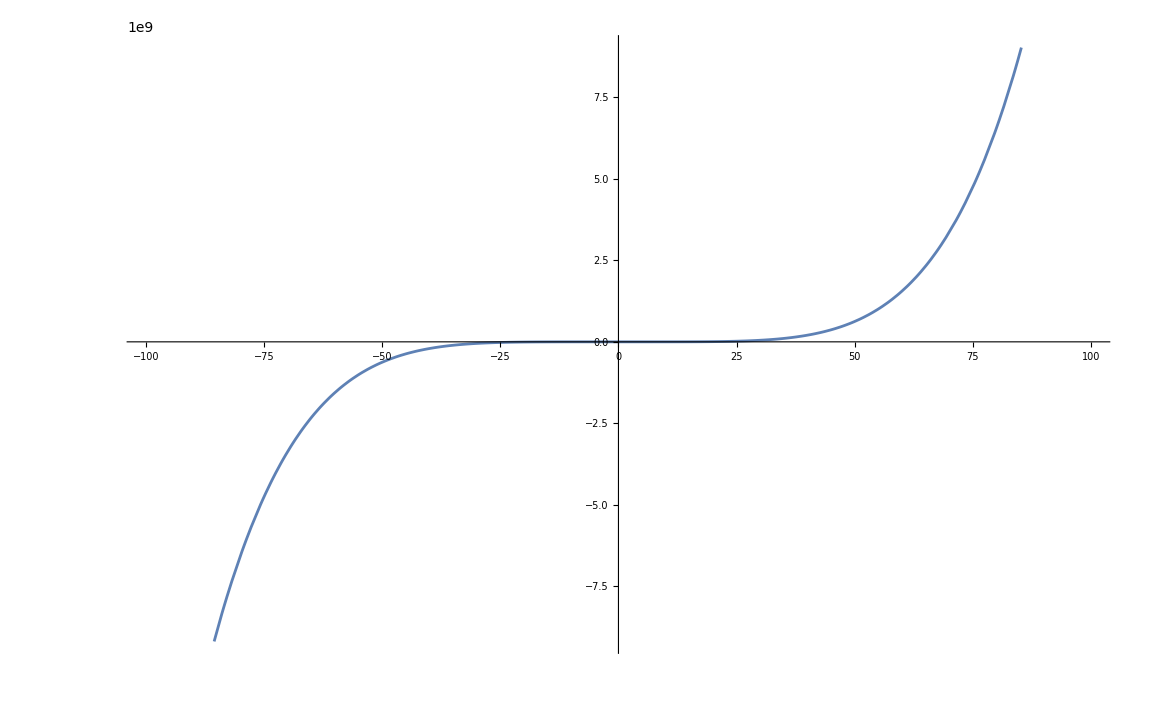

```mathematica
Plot[eqn[x]/.replace$mu$Params,{x,-100,100}]
```

```mathematica
n
```

1

```mathematica
Clear[bw,δE]
(*  the BW code assumes that the potential v0(x) is at a local mini-mum when the argument is equal to zero. *) 
bw=BenderWu[{V0[qStar+ξ]-V0[qStar],V2[qStar+ξ]},ξ,
(*level number*)n,
 (*perturbative order in g^2=ħ*) 5  ];
(* n=1, hbar order = 1 *)
δE[1,1]==(δE[1,1]=BWProcess[bw,Output->"Energy",OutputStyle->"Series"]/.replace$mu$Params)
```

δE[1,1]==2.1205-0.626871 g^2-0.202535 g^4-0.184631 g^6-0.243222 g^8-(0.406954+0. ⅈ) g^10

```mathematica
bw
```

{Join[{0.},{0.+3/2 √(2.+2. mu0)},√(2.+2. mu0) Table[(BenderWu`Private`epsilon$158295⟦BenderWu`Private`i$158295⟧)/(BenderWu`Private`omega$158295)^(BenderWu`Private`i$158295),{BenderWu`Private`i$158295,1,ord}]],Table[BenderWu`Private`A$158295⟦BenderWu`Private`lp,BenderWu`Private`k$158295⟧ (√(BenderWu`Private`omega$158295))^(BenderWu`Private`k$158295-BenderWu`Private`lp),{BenderWu`Private`lp,1,1+2 ord},{BenderWu`Private`k$158295,1,n+3 BenderWu`Private`lmax$158295+1}],{ξ,1,2 ord,0}}

```mathematica
E1guess[h_]:=δE[1,1]/.g^2->h
```

```mathematica
E1guess[2]
```

4.87068+0.0107546 ⅈ

## Analytic attempt using μ_eff and leaving the root uneval’d

```mathematica
Clear[V0,V1,q,z,mu0,mu1,s,q0,muEff,omega,ord,n];

V0[q_]:=Sin[q]^2+(mu0+mu1 Sin[q])/Cos[q]^2;
V1[q_]:=-I Sqrt[2] s Sin[q];
dV0[q_]:=mu1 Sec[q]+2 Cos[q] Sin[q]+2 Sec[q]^2 (mu0+mu1 Sin[q]) Tan[q]

(*Choose the well you want;seed near the symmetric minimum if needed*)
q0=q/. FindRoot[(dV0[q]/.replace$mu$Params/.s->-2)==0,{q,0}]

muEff=Simplify[V0[q0]]
omega=Simplify[Sqrt[D[V0[q],{q,2}]/. q->q0]];

V0BW[z_]:=Expand[V0[q0+z]-muEff];
V2BW[z_]:=Expand[V1[q0+z]-V1[q0]];

BW=BenderWu[{V0BW[z],V2BW[z]},z,1,1];

epsHat=BWProcess[BW,Output->"Energy",OutputStyle->"Series"];
```

0.00040031

1.60248×10^-7+1. mu0+0.00040031 mu1

```mathematica
ClearAll[P,x0,r0,z,muEff,V0BW,V1BW,V2BW,sinShift,cosShift,bw, q0,muEff, omega,q,V0,V1,dV0];

computeEpsHat[] := Module[{P,r0,sinShift,cosShift, V0BW,V1BW,bw,epsHat,muEff},

(*Stationary-point polynomial in x=Sin[q]*)
P[x_]:=2 x^5-4 x^3+mu1 x^2+2 (1+mu0) x+mu1;

(*Choose the branch/well by an exact algebraic root*)
(*x0[k_Integer]:=Root[P[#]&,k];*)

(*Cos[q0],with q0=ArcSin[x0],but never introduce ArcSin explicitly*)
r0[k_Integer]:=Sqrt[1-x0[k]^2];

(*Classical well bottom*)
muEff[k_Integer]:=x0[k]^2+(mu0+mu1 x0[k])/(1-x0[k]^2); 

(*Shift formulas*)sinShift[k_Integer][z_]:=x0[k] Cos[z]+r0[k] Sin[z];
cosShift[k_Integer][z_]:=r0[k] Cos[z]-x0[k] Sin[z];

(*Classical BW piece:subtract the well bottom*)
V0BW[k_Integer][z_]:=FullSimplify[sinShift[k][z]^2+(mu0+mu1 sinShift[k][z])/cosShift[k][z]^2-muEff[k]];

(*Quantum BW piece:subtract the constant term too*)
V1BW[k_Integer][z_]:=FullSimplify[-I Sqrt[2] s (sinShift[k][z]-x0[k])];
bw=BenderWu[{V0BW[1][z],V1BW[1][z]},z,1,1];
(* BW reduced energy ϵ̂ = (E-Subscript[μ, eff])/g^2 - Subscript[V, 1](x_*) *)
epsHat=BWProcess[bw,Output->"Energy",OutputStyle->"Series"]; 
epsHat
]
```

```mathematica
computeEpsHat[]/.x0[1]->0
```

3/2 √(2+2 mu0)+g^2 (-(ⅈ s ((10 mu1)/(3 (2+2 mu0))-(2 ⅈ √2 s)/(√(2+2 mu0))))/(√2 √(2+2 mu0))-3/4 (-(5 mu1 ((10 mu1)/(3 (2+2 mu0))-(2 ⅈ √2 s)/(√(2+2 mu0))))/(6 (2+2 mu0))+(ⅈ √2 s (-(10 mu1)/(3 (2+2 mu0))+(2 ⅈ √2 s)/(√(2+2 mu0))))/(√(2+2 mu0))+5/2 ((175 mu1^2)/(108 (2+2 mu0)^2)-(5 ⅈ √2 mu1 s)/(9 (2+2 mu0)^(3/2))-2 ((-8+16 mu0)/(24 (2+2 mu0))+(5 mu1 (-(10 mu1)/(3 (2+2 mu0))+(2 ⅈ √2 s)/(√(2+2 mu0))))/(12 (2+2 mu0))))))

```mathematica
ClearAll[x0,r0,z,mu0,mu1,s,g,ν,ord,P,muEff,sinShift,cosShift,V0BW,V1BW,reduceRules,reduceExpr, bw, epsHat];

(*Stationary-point polynomial for x0=Sin[q0]*)
P[x_]:=2 x^5-4 x^3+mu1 x^2+2 (1+mu0) x+mu1;

(*Formal algebraic relations*)
reduceRules={r0^2->1-x0^2,x0^5->2 x0^3-(mu1/2) x0^2-(1+mu0) x0-mu1/2};

reduceExpr[expr_]:=FixedPoint[Expand[#/. reduceRules]&,expr];

(*Classical well bottom*)
muEff=x0^2+(mu0+mu1 x0)/(1-x0^2);

(*Shift formulas*)
sinShift[z_]:=x0 Cos[z]+r0 Sin[z];
cosShift[z_]:=r0 Cos[z]-x0 Sin[z]; (* r0^2 = 1 -x0^2 *)

(*BW input pieces*)
V0BW[z_]:=reduceExpr@FullSimplify[sinShift[z]^2+(mu0+mu1 sinShift[z])/cosShift[z]^2-muEff];

V1BW[z_]:=reduceExpr@FullSimplify[-I Sqrt[2] s (sinShift[z]-x0)];
```

```mathematica
(* build BW object *)
```

```mathematica
bw=BenderWu[{V0BW[z],V1BW[z]},z,0,1,Simplify->True ];
(* BW reduced energy ϵ̂ = (E-Subscript[μ, eff])/g^2 - Subscript[V, 1](x_*) *)
epsHat=BWProcess[bw,Output->"Energy",OutputStyle->"Series"];
```

```mathematica
symmetricLimit[f_]:=f/.{s->0,mu1->0,x0->0,r0->1}
```

```mathematica
symmetricLimit[epsHat]
```

1/2 √(2+2 mu0)+(g^2 (-144+144 mu0+288 mu0^2))/(288 (2+2 mu0)^2)

```mathematica
Eseries=reduceExpr@Expand[muEff+g^2 (-I Sqrt[2] s x0+epsHat)];
```

```mathematica
xRootSub[branch_IntegerQ][mu0val_NumericQ,mu1val_NumericQ]:=x0->Root[P[#]/. {mu0->mu0val,mu1->mu1val}&,branch]
rRootSub[branch_IntegerQ][mu0val_NumericQ,mu1val_NumericQ]:=r0->Sqrt[ 1-Root[P[#]/. {mu0->mu0val,mu1->mu1val}&,branch]^2 ]
```

```mathematica
rootsub[branchk_][mu0val_,mu1val_,f_]:=Module[{x0k,r0k,f1,f2,f3},
f1=f/.x0->x0k;
f2=f1/.r0->Sqrt[1-x0k^2];
f3=f2/. x0k->Root[P[#]/. {mu0->mu0val,mu1->mu1val}&,branchk];
f3/.mu0->mu0val/.mu1->mu1val
]
```

```mathematica
rootsub[1][mu0val,mu1val,Eseries]/.s->-2
rootsub[2][mu0val,mu1val,Eseries]/.s->-2
```

-0.000775160124147513706911309477640688751034907237226+(0.70683232749542375299995919123067808147569362412037002+0.00113224888696850632659268248491658651366560930373 ⅈ) g^2+(1.876261374662001504784082749044463575065208934305044+0.0016037293974636524424354106161708946718006110765 ⅈ) g^4

0.92103151016183766766651273367771642118670546751+4.157523020888361738596147186165254282681256352 ⅈ g^2+1.712431043345553826150133745902156516688041 g^4

## Numerical Bohr-Sommerfeld recursion

```mathematica
WKBprec=rootPrec;
```

```mathematica
ClearAll[Vcl,V1,Q0,Q1,pCoeff,ξ,p0,p1,p2];

Vcl[q_,mu0_,mu1_]:=Cos[q]^2+mu0/Cos[q]^2;
V1[q_,mu1_,mu2_]:=mu2 Sin[q] +mu1 Sin[q]/Cos[q]^2;;

Q0[q_,Es_,mu0_,mu1_]:=2 (Es-Vcl[q,mu0,mu1]);
Q1[q_,mu1_,mu2_]:=-2 V1[q,mu1,mu2];

(*WKB coefficients for P^2+ε P'=Q0+ε Q1*)

pCoeff[0,q_,Es_,mu0_,mu1_,s_]:=Sqrt[Q0[q,Es,mu0,mu1]];

pCoeff[1,q_,Es_,mu0_,mu1_,mu2_]:=pCoeff[1,q,Es,mu0,mu1,mu2]=FullSimplify[(Q1[q,mu1,mu2]-(D[pCoeff[0,ξ,Es,mu0,mu1,mu2],ξ]/. ξ->q))/(2 pCoeff[0,q,Es,mu0,mu1,mu2])];

pCoeff[n_Integer?Positive,q_,Es_,mu0_,mu1_,mu2_]/;n>=2:=pCoeff[n,q,Es,mu0,mu1,mu2]=Module[{deriv,quad},
deriv=D[pCoeff[n-1,ξ,Es,mu0,mu1,mu2],ξ]/. ξ->q;
quad=Sum[pCoeff[j,q,Es,mu0,mu1,mu2] pCoeff[n-j,q,Es,mu0,mu1,mu2],{j,1,n-1}];
FullSimplify[-(deriv+quad)/(2 pCoeff[0,q,Es,mu0,mu1,mu2])]];

p0[q_,Es_,mu0_,mu1_,mu2_]:=pCoeff[0,q,Es,mu0,mu1,mu2];
p1[q_,Es_,mu0_,mu1_,mu2_]:=pCoeff[1,q,Es,mu0,mu1,mu2];
p2[q_,Es_,mu0_,mu1_,mu2_]:=pCoeff[2,q,Es,mu0,mu1,mu2];
```

```mathematica
ClearAll[openSegmentIntegral,closedCycleCoeff];

openSegmentIntegral[f_,{qa_?NumericQ,qb_?NumericQ},opts:OptionsPattern[NIntegrate]]:=NIntegrate[Evaluate[2 (qb-qa) Sin[t] Cos[t] f[qa+(qb-qa) Sin[t]^2]],{t,0,Pi/2},WorkingPrecision->40,AccuracyGoal->18,PrecisionGoal->18,MaxRecursion->20,Method->{"GlobalAdaptive","SymbolicProcessing"->0},opts];

closedCycleCoeff[n_Integer,seg:{qa_?NumericQ,qb_?NumericQ},E_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=2 openSegmentIntegral[Function[q,Evaluate[pCoeff[n,q,E,mu0,mu1,mu2]]],seg];
```

```mathematica
wkbParams=τ2params[[10]];
someroots=quarticRoots[wkbParams["Es"],wkbParams["μ0"],wkbParams["μ1"], wkbParams["μ2"]]
```

NSolveValues::precw: The precision of the argument function ({0.0204492500236249199981306530115325217009672839392+0.0408 x$164702+0.9803257499763750800018693469884674782990327160608 x$164702^2-0.04 x$164702^3-x$164702^4}) is less than WorkingPrecision (50).

{-0.99998724545764664947370866198150237776406444624815,-0.02037742563075773281849291964184326895325571657849-0.14148889394888991666870015925634799833652176173462 ⅈ,-0.02037742563075773281849291964184326895325571657849+0.14148889394888991666870015925634799833652176173462 ⅈ,1.0007420967191621151106945012651889156705758794051}

We see that the turning points come in conjugate pairs of the ordered set

```mathematica
MaTeX["\\text{ The roots have the form } \\{e_1,e_2,e_3,e_4\\}= \\{-1,a,\\bar{a},1\\} "]
MaTeX["\\text{ The cross ratio: \ \    } \ m(e_1,e_2,e_3,e_4) = \\frac{ (e_2-e_1)(e_4-e_3) }{ (e_3-e_1)(e_4-e_2) } \\text{ and the numerator and denominator are conjugate which makes \ \ } \  \ \vert{m}\vert \approx 1 \\text{ which is a delicate branch numerically so we pair them as a real pair and a conjugate pair, and define the cycles from those cuts.}"]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[turningPointsQ];

turningPointsQ[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:60]:=Module[{xr,xL,xR,qL,qR,qAdjL,qAdjR},
xr=quarticRoots[Es,mu0,mu1,mu2,wp];
{xL,xR}=xr[[1;;2]];
qL=ArcSin[xL];
qR=ArcSin[xR];
(*turning points in the adjacent right-hand strip*)qAdjL=Pi-qR;
qAdjR=Pi-qL;
<|"xL"->xL,"xR"->xR,"qL"->qL,"qR"->qR,"qAdjL"->qAdjL,"qAdjR"->qAdjR|>]

ClearAll[ABsegmentsQ];

ABsegmentsQ[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:60]:=Module[{tp},tp=turningPointsQ[Es,mu0,mu1,mu2,wp];
<|"Aseg"->{tp["qL"],tp["qR"]},"Bseg"->{tp["qR"],tp["qAdjL"]},"data"->tp|>]
```

```mathematica
ClearAll[NA0fromRoots,NB0fromRoots];

NA0fromRoots[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:60]:=Module[{seg},seg=ABsegmentsQ[Es,mu0,mu1,mu2,wp]["Aseg"];
closedCycleCoeff[0,seg,Es,mu0,mu1,mu2]]

NB0fromRoots[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:60]:=Module[{seg},seg=ABsegmentsQ[Es,mu0,mu1,mu2,wp]["Bseg"];
closedCycleCoeff[0,seg,Es,mu0,mu1,mu2]]
```

```mathematica
ClearAll[openSegmentIntegral,closedCycleCoeff];

openSegmentIntegral[f_,{qa_?NumericQ,qb_?NumericQ},opts:OptionsPattern[NIntegrate]]:=NIntegrate[Evaluate[2 (qb-qa) Sin[t] Cos[t] f[qa+(qb-qa) Sin[t]^2]],{t,0,Pi/2},WorkingPrecision->40,AccuracyGoal->18,PrecisionGoal->18,MaxRecursion->20,Method->{"GlobalAdaptive","SymbolicProcessing"->0},opts];

closedCycleCoeff[n_Integer,seg:{qa_?NumericQ,qb_?NumericQ},Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=2 openSegmentIntegral[Function[q,Evaluate[pCoeff[n,q,Es,mu0,mu1,mu2]]],seg];
```

```mathematica
ClearAll[NAcoeff,NBcoeff];

NAcoeff[n_Integer,Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:60]:=Module[{seg},seg=ABsegmentsQ[Es,mu0,mu1,mu2,wp]["Aseg"];
closedCycleCoeff[n,seg,Es,mu0,mu1,mu2]]

NBcoeff[n_Integer,Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,wp_:60]:=Module[{seg},seg=ABsegmentsQ[Es,mu0,mu1,mu2,wp]["Bseg"];
closedCycleCoeff[n,seg,Es,mu0,mu1,mu2]]
```

```mathematica
NAcoeff[2,E2vals[[10]],μ0vals[[1]],μ1vals[[1]],-2]
```

NSolveValues::precw: The precision of the argument function ({0.09541265966905383391488461113756170847937744217578010070576+2.08 x$166082+0.98208734033094616608511538886243829152062255782421989929424 x$166082^2-2. x$166082^3-x$166082^4}) is less than WorkingPrecision (60).

NIntegrate::precw: The precision of the argument function (-(«1»)/((-0.0775-«79» Cosh[«1»]^2+Cosh[(«97»+«1»)-«1»]^4)^3)) is less than WorkingPrecision (40.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in t near {t} = {1.146490347963637221629837763420862319429}. NIntegrate obtained -2.163735489096537117557268695860260091586×10^11-1.268254668608304462275654361143939172099×10^10 ⅈ and 2.058579523109911099933432449403101245332×10^11 for the integral and error estimates.

-4.327470978193074235114537391720520183173×10^11-2.536509337216608924551308722287878344198×10^10 ⅈ

```mathematica
ClearAll[d1,E0Quant,E1Quant];

d1[f_,E0_?NumericQ,h_:10^-5]:=(f[E0+h]-f[E0-h])/(2 h);

E0Quant[l_Integer,hbar_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ,wp_:60]:=Es/. FindRoot[NAcoeff[0,Es,mu0,mu1,mu2,wp]==2 Pi hbar (l+1/2),{Es,Eguess},WorkingPrecision->30];

E1Quant[l_Integer,hbar_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ,wp_:60]:=Module[{E0,f0,f1},E0=E0Quant[l,hbar,mu0,mu1,mu2,Eguess,wp];
f0[x_?NumericQ]:=NAcoeff[0,x,mu0,mu1,mu2,wp];
f1[x_?NumericQ]:=NAcoeff[1,x,mu0,mu1,mu2,wp];
-f1[E0]/d1[f0,E0]]
```

```mathematica
ClearAll[d1,E0Quant,E1Quant];

d1[f_,E0_?NumericQ,h_:10^-5]:=(f[E0+h]-f[E0-h])/(2 h);

E0Quant[l_Integer,hbar_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ,wp_:60]:=Es/. FindRoot[NAcoeff[0,Es,mu0,mu1,mu2,wp]==2 Pi hbar (l+1/2),{Es,Eguess},WorkingPrecision->30];

E1Quant[l_Integer,hbar_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ,wp_:60]:=Module[{E0,f0,f1},E0=E0Quant[l,hbar,mu0,mu1,mu2,Eguess,wp];
f0[x_?NumericQ]:=NAcoeff[0,x,mu0,mu1,mu2,wp];
f1[x_?NumericQ]:=NAcoeff[1,x,mu0,mu1,mu2,wp];
-f1[E0]/d1[f0,E0]]
```

```mathematica
ClearAll[NBtildeFirstOrder];

NBtildeFirstOrder[l_Integer,hbar_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ,wp_:60]:=Module[{E0,E1,g0,g1},E0=E0Quant[l,hbar,mu0,mu1,mu2,Eguess,wp];
E1=E1Quant[l,hbar,mu0,mu1,mu2,Eguess,wp];
g0[x_?NumericQ]:=NBcoeff[0,x,mu0,mu1,mu2,wp];
g1[x_?NumericQ]:=NBcoeff[1,x,mu0,mu1,mu2,wp];
g0[E0]+hbar (g1[E0]+E1 d1[g0,E0])]
```

```mathematica
Table[{h,NBtildeFirstOrder[0,h,mu0val,mu1val,mu2val,E1guess[h]]},{h,{0.08,0.06,0.04,0.03}}]
```

{{0.08,NBtildeFirstOrder[0,0.08,-0.000775,-0.0008,-0.04,E1guess[0.08]]},{0.06,NBtildeFirstOrder[0,0.06,-0.000775,-0.0008,-0.04,E1guess[0.06]]},{0.04,NBtildeFirstOrder[0,0.04,-0.000775,-0.0008,-0.04,E1guess[0.04]]},{0.03,NBtildeFirstOrder[0,0.03,-0.000775,-0.0008,-0.04,E1guess[0.03]]}}

```mathematica
(*  turning points*)

qL=rootsTracked[[1]];
qR=rootsTracked[[2]];
qNextL=rootsTracked[[3]];   (*left turning point of the neighboring well*)

Aseg={qL,qR};
Bseg={qR,qNextL};

NA0[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=closedCycleCoeff[0,Aseg,Es,mu0,mu1,mu2];

NA1[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=closedCycleCoeff[1,Aseg,Es,mu0,mu1,mu2];

NA2[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=closedCycleCoeff[2,Aseg,Es,mu0,mu1,mu2];

NB0[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=closedCycleCoeff[0,Bseg,Es,mu0,mu1,mu2];

NB1[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=closedCycleCoeff[1,Bseg,Es,mu0,mu1,mu2];

NB2[Es_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=closedCycleCoeff[2,Bseg,Es,mu0,mu1,mu2];
```

```mathematica
ClearAll[NBtilde0,NBtilde1,NBtilde2];

NBtilde0[J_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ]:=Module[{E0},E0=E0fromJ[J,mu0,mu1,s,Eguess];
NB0[E0,mu0,mu1,mu2]];

NBtilde1[J_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ]:=Module[{E0,E1,g0,g1},E0=E0fromJ[J,mu0,mu1,mu2,Eguess];
E1=E1fromJ[J,mu0,mu1,s,Eguess];
g0[x_?NumericQ]:=NB0[x,mu0,mu1,mu2];
g1[x_?NumericQ]:=NB1[x,mu0,mu1,mu2];
g1[E0]+E1 d1[g0,E0]];

NBtilde2[J_?NumericQ,mu0_?NumericQ,mu1_?NumericQ,mu2_?NumericQ,Eguess_?NumericQ]:=Module[{E0,E1,E2,g0,g1,g2},E0=E0fromJ[J,mu0,mu1,mu2,Eguess];
E1=E1fromJ[J,mu0,mu1,mu2,Eguess];
E2=E2fromJ[J,mu0,mu1,mu2,Eguess];
g0[x_?NumericQ]:=NB0[x,mu0,mu1,mu2];
g1[x_?NumericQ]:=NB1[x,mu0,mu1,mu2];
g2[x_?NumericQ]:=NB2[x,mu0,mu1,mu2];
g2[E0]+E1 d1[g1,E0]+E2 d1[g0,E0]+(E1^2/2) d2[g0,E0]];
```